# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 30000/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
bBzSKA=bmeanzSKA+dbz/2;
bFzSKA=bmeanzSKA-dbz/2;
bTzSKA=(bBzSKA+bFzSKA)/2;
```

```mathematica
bBzSKA
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bB0=b1+db/2
bF0=b1-db/2
```

1.054

0.054

```mathematica
b1B=b1;
b1F=b1;
b2B=b2;
b2F=b2;
```

```mathematica
b1B
```

0.554

Import CAMB results

```mathematica
Length[zsigma]
```

100

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=zsigma[[All,2]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.814468

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.627151

```mathematica
sigma8z[0.5]
```

0.627168

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

Need of fevolB and fevolF

```mathematica
bBtildezSKA=bBzSKA D1zSKA Sigma8z0/D10
bFtildezSKA=bFzSKA D1zSKA Sigma8z0/D10
```

{0.845096,0.837813,0.832225,0.828564,0.826993,0.827618,0.830509,0.835711,0.843256,0.853172,0.865485,0.880225,0.897432,0.917153,0.939447,0.964384,0.992045,1.02253,1.05594}

{0.0925901,0.124044,0.154884,0.185276,0.2154,0.245446,0.275603,0.306056,0.336987,0.368571,0.400978,0.434376,0.468928,0.5048,0.542155,0.581158,0.62198,0.664792,0.709776}

```mathematica
bBtildezSKA-bFtildezSKA
```

{0.752505,0.713769,0.677341,0.643289,0.611593,0.582172,0.554906,0.529655,0.50627,0.484602,0.464507,0.44585,0.428504,0.412353,0.397292,0.383225,0.370065,0.357734,0.346161}

```mathematica
(bBtildezSKA+bFtildezSKA)/2
```

{0.468843,0.480929,0.493555,0.50692,0.521196,0.536532,0.553056,0.570883,0.590122,0.610871,0.633231,0.6573,0.68318,0.710977,0.740801,0.772771,0.807012,0.843659,0.882856}

# Multi-SPLIT Covariance

## Covariance Blocks

## Parameters

### Galaxy bias

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bT[m_,dbz_]:=bmeanzSKA ;
```

#### Standard splitting 50% (m = 2)

```mathematica
m = 2;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA50=bB[2, dbz]
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA50=bF[2,dbz]
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bTzSKA50 = bT[2,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA50 = 1/2;
```

```mathematica
smodelBzSKA50 = List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
```

```mathematica
fevolBzSKA50 = List[3.00956639,0.07976877,-0.81552783,-0.6173486,-0.39242556,-0.31155665,-0.26595514,-0.1091582,0.07791229,0.18253319,0.17336397,0.03980399,-0.12308668,-0.28681099,-0.41997146,-0.51728093,-0.57341237,-0.57764042,-0.55234844];
```

FAINT

```mathematica
nFSKA50 = 1/2;
```

```mathematica
smodelzSKA50 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA50);]
```

```mathematica
m
```

2

```mathematica
smodelFzSKA50 = (m/(m-1)) smodelzSKA50 -(1/(m-1)) smodelBzSKA50
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
fevolFzSKA50 = List[1.49669846,4.74321837,4.48561914,3.00325909,1.42466759,0.23953114,-0.63019961,-1.38888192,-2.01572455,-2.47043394,-2.7319998,-2.83059041,-2.87381247,-2.89939059,-2.94565432,-3.01777315,-3.12068025,-3.25274921,-3.36209773];
```

#### Splitting with 20% Bright (m=5)

```mathematica
m=5;
```

```mathematica
db=1.3;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA30=bB[5, dbz]
```

{1.66304,1.71379,1.76867,1.82801,1.89219,1.9616,2.03666,2.11784,2.20563,2.30056,2.40323,2.51426,2.63434,2.76419,2.90462,3.05649,3.22073,3.39834,3.59042}

```mathematica
bFzSKA30=bF[5,dbz]
```

{0.363042,0.413787,0.468665,0.528013,0.592194,0.661603,0.736665,0.81784,0.905627,1.00056,1.10323,1.21426,1.33434,1.46419,1.60462,1.75649,1.92073,2.09834,2.29042}

```mathematica
bTzSKA30 = bT[5,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA30 = 1/5;
```

```mathematica
smodelBzSKA30 = List[0.67305899,0.47850262,0.60568693,0.63024073,0.72531868,0.79127179,0.84909062,0.89625832,0.94479023,1.00555245,1.07651371,1.15262299,1.23144197,1.31168461,1.39252626,1.47460293,1.55787663,1.64185011,1.72636861];
```

```mathematica
fevolBzSKA30 = List[-6.53972086,0.09057049,-0.5804842,-0.04639725,-0.41476509,-0.26788556,0.01445244,0.42731939,0.81266783,1.02409595,1.1320267,1.19388959,1.25350597,1.31588318,1.39584288,1.48600484,1.58671907,1.71015017,1.84649527];
```

FAINT

```mathematica
nFSKA30 = 4/5;
```

```mathematica
smodelzSKA30 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA30);]
m
```

5

```mathematica
smodelFzSKA30 = (m/(m-1)) smodelzSKA30 -(1/(m-1)) smodelBzSKA30
```

{-0.0416801,0.0903066,0.155976,0.267966,0.373166,0.486556,0.596786,0.706258,0.813062,0.915465,1.01639,1.11722,1.2207,1.32603,1.43465,1.54638,1.6611,1.77922,1.89705}

```mathematica
fevolFzSKA30 = List[4.45134575,2.99172434,2.43892812,1.50279337,0.74884254,0.02195544,-0.56370983,-1.04310492,-1.41429962,-1.68596196,-1.88215407,-2.04271391,-2.18643846,-2.32034678,-2.45247683,-2.58091001,-2.70548765,-2.82153106,-2.90815267];
```

### Survey

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
nBzSKA50=Table[nBSKA50, {i,Length[zSKA]}];
nFzSKA50=Table[nFSKA50, {i,Length[zSKA]}];
nBzSKA30=Table[nBSKA30, {i,Length[zSKA]}];
nFzSKA30=Table[nFSKA30, {i,Length[zSKA]}];
```

```mathematica
nBzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nFzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nBzSKA30
```

{1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5}

```mathematica
nFzSKA30
```

{4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5}

```mathematica
NbarBzSKA50=NbarzSKA*nBzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarFzSKA50=NbarzSKA*nFzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarBzSKA30=NbarzSKA*nBzSKA30
```

{0.0400337,0.0234391,0.0139472,0.00845873,0.00521084,0.00329955,0.00211145,0.00136244,0.000878159,0.000561763,0.000359012,0.000227934,0.000143346,0.000089753,0.0000552078,0.0000335766,0.000020146,0.0000118164,6.7799×10^-6}

```mathematica
NbarFzSKA30=NbarzSKA*nFzSKA30
```

{0.160135,0.0937563,0.0557889,0.0338349,0.0208434,0.0131982,0.00844582,0.00544975,0.00351263,0.00224705,0.00143605,0.000911735,0.000573386,0.000359012,0.000220831,0.000134307,0.000080584,0.0000472656,0.0000271196}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50/nBzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffFSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA50/nFzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffBSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA30/nBzSKA30
```

{4.3512×10^-8,2.72818×10^-8,2.36319×10^-8,2.38493×10^-8,2.62978×10^-8,3.02587×10^-8,3.62305×10^-8,4.46839×10^-8,5.68217×10^-8,7.4538×10^-8,9.97686×10^-8,1.36572×10^-7,1.91266×10^-7,2.7211×10^-7,3.97903×10^-7,5.93433×10^-7,9.03721×10^-7,1.41692×10^-6,2.28394×10^-6}

```mathematica
coeffFSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA30/nFzSKA30
```

{1.0878×10^-8,6.82046×10^-9,5.90797×10^-9,5.96232×10^-9,6.57444×10^-9,7.56467×10^-9,9.05763×10^-9,1.1171×10^-8,1.42054×10^-8,1.86345×10^-8,2.49422×10^-8,3.41429×10^-8,4.78164×10^-8,6.80274×10^-8,9.94757×10^-8,1.48358×10^-7,2.2593×10^-7,3.5423×10^-7,5.70985×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA50=(5smodelBzSKA50 +(2-5smodelBzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA50)fzSKA
```

{3.03044,1.96942,1.50533,1.08587,0.778835,0.633417,0.577577,0.500896,0.433983,0.449219,0.574176,0.83023,1.14574,1.49666,1.85103,2.19899,2.5307,2.83137,3.11887}

```mathematica
cFzSKA50=(5smodelFzSKA50 +(2-5smodelFzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA50)fzSKA
```

{8.73219,3.49283,1.72274,1.11051,1.14024,1.34369,1.62634,2.0112,2.43762,2.84422,3.1753,3.42655,3.6648,3.91551,4.20934,4.55135,4.94709,5.39644,5.84627}

```mathematica
cBzSKA30=(5smodelBzSKA30 +(2-5smodelBzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA30)fzSKA
```

{0.135889,0.503592,0.157979,0.0547954,0.161839,0.113743,0.00690671,-0.175739,-0.34887,-0.395523,-0.351197,-0.249399,-0.125327,0.0159835,0.158835,0.307728,0.460774,0.604806,0.747542}

```mathematica
cFzSKA30=(5smodelFzSKA30 +(2-5smodelFzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA30)fzSKA
```

{7.31767,3.28801,1.97805,1.35904,1.15896,1.20726,1.37572,1.61399,1.88197,2.15728,2.43122,2.72283,3.03792,3.37861,3.74802,4.14203,4.55843,4.99118,5.41633}

### Elements

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
G[1,3,3,3]
```

24/385

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2corrCC[n,m]coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

4

```mathematica
4 i /. i -> 43
```

172

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

Monopole 50  - Monopole 50

```mathematica
coeffvarCCpop50pop30BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{9.88444×10^-9,3.89227×10^-9,2.14549×10^-9,1.40253×10^-9,1.01794×10^-9,7.93965×10^-10,6.53364×10^-10,5.60849×10^-10,4.9843×10^-10,4.56187×10^-10,4.28343×10^-10,4.11417×10^-10,4.03291×10^-10,4.02713×10^-10,4.09023×10^-10,4.21995×10^-10,4.41763×10^-10,4.68776×10^-10,5.03793×10^-10}

```mathematica
coeffvarCCpop30pop50BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{9.88444×10^-9,3.89227×10^-9,2.14549×10^-9,1.40253×10^-9,1.01794×10^-9,7.93965×10^-10,6.53364×10^-10,5.60849×10^-10,4.9843×10^-10,4.56187×10^-10,4.28343×10^-10,4.11417×10^-10,4.03291×10^-10,4.02713×10^-10,4.09023×10^-10,4.21995×10^-10,4.41763×10^-10,4.68776×10^-10,5.03793×10^-10}

```mathematica
coeffvarCCpop50pop30FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.21262×10^-10,6.62898×10^-11,4.82628×10^-11,4.01586×10^-11,3.60832×10^-11,3.41138×10^-11,3.34784×10^-11,3.38368×10^-11,3.50449×10^-11,3.7065×10^-11,3.9928×10^-11,4.37197×10^-11,4.85759×10^-11,5.46859×10^-11,6.23002×10^-11,7.1742×10^-11,8.34241×10^-11,9.78712×10^-11,1.15748×10^-10}

```mathematica
coeffvarCCpop30pop50FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.21262×10^-10,6.62898×10^-11,4.82628×10^-11,4.01586×10^-11,3.60832×10^-11,3.41138×10^-11,3.34784×10^-11,3.38368×10^-11,3.50449×10^-11,3.7065×10^-11,3.9928×10^-11,4.37197×10^-11,4.85759×10^-11,5.46859×10^-11,6.23002×10^-11,7.1742×10^-11,8.34241×10^-11,9.78712×10^-11,1.15748×10^-10}

```mathematica
varCCMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCCpop50pop30BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCCpop30pop50BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCCpop50pop30FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
varCCMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCCpop30pop50FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

```mathematica
coeffvarCCpop50BFpop30BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{9.75184×10^-10,4.61763×10^-10,2.97293×10^-10,2.22177×10^-10,1.81404×10^-10,1.57224×10^-10,1.42403×10^-10,1.33524×10^-10,1.28823×10^-10,1.27345×10^-10,1.28582×10^-10,1.32298×10^-10,1.38443×10^-10,1.47114×10^-10,1.58534×10^-10,1.73054×10^-10,1.91158×10^-10,2.13485×10^-10,2.40859×10^-10}

```mathematica
coeffvarCCpop30BFpop50BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{9.75184×10^-10,4.61763×10^-10,2.97293×10^-10,2.22177×10^-10,1.81404×10^-10,1.57224×10^-10,1.42403×10^-10,1.33524×10^-10,1.28823×10^-10,1.27345×10^-10,1.28582×10^-10,1.32298×10^-10,1.38443×10^-10,1.47114×10^-10,1.58534×10^-10,1.73054×10^-10,1.91158×10^-10,2.13485×10^-10,2.40859×10^-10}

```mathematica
varCCMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.24729×10^-9,1.37689×10^-9,8.09675×10^-10,5.60563×10^-10,4.2843×10^-10,3.50304×10^-10,3.01111×10^-10,2.69208×10^-10,2.48589×10^-10,2.35931×10^-10,2.29325×10^-10,2.27664×10^-10,2.30345×10^-10,2.37108×10^-10,2.47946×10^-10,2.63068×10^-10,2.82882×10^-10,3.07999×10^-10,3.39256×10^-10}

```mathematica
coeffvarCC30BFx50B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{3.24729×10^-9,1.37689×10^-9,8.09675×10^-10,5.60563×10^-10,4.2843×10^-10,3.50304×10^-10,3.01111×10^-10,2.69208×10^-10,2.48589×10^-10,2.35931×10^-10,2.29325×10^-10,2.27664×10^-10,2.30345×10^-10,2.37108×10^-10,2.47946×10^-10,2.63068×10^-10,2.82882×10^-10,3.07999×10^-10,3.39256×10^-10}

```mathematica
coeffvarCC50Fx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.22473×10^-10,1.66864×10^-10,1.15777×10^-10,9.22857×10^-11,7.97468×10^-11,7.27227×10^-11,6.89909×10^-11,6.75175×10^-11,6.77942×10^-11,6.95812×10^-11,7.2797×10^-11,7.74679×10^-11,8.37061×10^-11,9.17032×10^-11,1.01732×10^-10,1.14158×10^-10,1.29453×10^-10,1.48218×10^-10,1.71217×10^-10}

```mathematica
coeffvarCC30BFx50F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{3.22473×10^-10,1.66864×10^-10,1.15777×10^-10,9.22857×10^-11,7.97468×10^-11,7.27227×10^-11,6.89909×10^-11,6.75175×10^-11,6.77942×10^-11,6.95812×10^-11,7.2797×10^-11,7.74679×10^-11,8.37061×10^-11,9.17032×10^-11,1.01732×10^-10,1.14158×10^-10,1.29453×10^-10,1.48218×10^-10,1.71217×10^-10}

```mathematica
coeffvarCC30Bx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.76574×10^-9,1.23278×10^-9,7.51902×10^-10,5.3511×10^-10,4.17787×10^-10,3.47388×10^-10,3.0264×10^-10,2.73518×10^-10,2.54788×10^-10,2.4353×10^-10,2.38057×10^-10,2.37396×10^-10,2.4103×10^-10,2.48755×10^-10,2.6061×10^-10,2.76839×10^-10,2.97882×10^-10,3.24383×10^-10,3.57211×10^-10}

```mathematica
coeffvarCC50BFx30B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.76574×10^-9,1.23278×10^-9,7.51902×10^-10,5.3511×10^-10,4.17787×10^-10,3.47388×10^-10,3.0264×10^-10,2.73518×10^-10,2.54788×10^-10,2.4353×10^-10,2.38057×10^-10,2.37396×10^-10,2.4103×10^-10,2.48755×10^-10,2.6061×10^-10,2.76839×10^-10,2.97882×10^-10,3.24383×10^-10,3.57211×10^-10}

```mathematica
coeffvarCC30Fx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{3.53639×10^-10,1.77556×10^-10,1.20391×10^-10,9.42502×10^-11,8.02788×10^-11,7.23536×10^-11,6.79793×10^-11,6.59941×10^-11,6.58216×10^-11,6.71816×10^-11,6.99653×10^-11,7.41791×10^-11,7.99182×10^-11,8.73586×10^-11,9.67578×10^-11,1.08464×10^-10,1.22929×10^-10,1.40736×10^-10,1.6262×10^-10}

```mathematica
coeffvarCC50BFx30F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.53639×10^-10,1.77556×10^-10,1.20391×10^-10,9.42502×10^-11,8.02788×10^-11,7.23536×10^-11,6.79793×10^-11,6.59941×10^-11,6.58216×10^-11,6.71816×10^-11,6.99653×10^-11,7.41791×10^-11,7.99182×10^-11,8.73586×10^-11,9.67578×10^-11,1.08464×10^-10,1.22929×10^-10,1.40736×10^-10,1.6262×10^-10}

```mathematica
varCCMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONO50Fx30BFLp4d4to172zSKA= Table[coeffvarCC50Fx30BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50FLp4d4to172zSKA= Table[coeffvarCC30BFx50F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BFLp4d4to172zSKA= Table[coeffvarCC30Fx50BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30FLp4d4to172zSKA= Table[coeffvarCC50BFx30F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.11133×10^-9,5.04723×10^-10,3.15114×10^-10,2.30055×10^-10,1.84442×10^-10,1.57555×10^-10,1.4104×10^-10,1.3099×10^-10,1.25396×10^-10,1.23171×10^-10,1.23728×10^-10,1.26781×10^-10,1.32244×10^-10,1.40186×10^-10,1.50807×10^-10,1.64434×10^-10,1.81528×10^-10,2.02705×10^-10,2.28759×10^-10}

```mathematica
coeffvarCCpop30Fpop50BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.11133×10^-9,5.04723×10^-10,3.15114×10^-10,2.30055×10^-10,1.84442×10^-10,1.57555×10^-10,1.4104×10^-10,1.3099×10^-10,1.25396×10^-10,1.23171×10^-10,1.23728×10^-10,1.26781×10^-10,1.32244×10^-10,1.40186×10^-10,1.50807×10^-10,1.64434×10^-10,1.81528×10^-10,2.02705×10^-10,2.28759×10^-10}

```mathematica
coeffvarCCpop50Fpop30BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{8.73513×10^-10,4.27817×10^-10,2.82704×10^-10,2.15647×10^-10,1.78986×10^-10,1.57213×10^-10,1.43962×10^-10,1.36214×10^-10,1.32406×10^-10,1.31698×10^-10,1.33648×10^-10,1.38068×10^-10,1.4494×10^-10,1.54388×10^-10,1.66659×10^-10,1.82127×10^-10,2.01298×10^-10,2.24839×10^-10,2.53599×10^-10}

```mathematica
coeffvarCCpop30Bpop50FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{8.73513×10^-10,4.27817×10^-10,2.82704×10^-10,2.15647×10^-10,1.78986×10^-10,1.57213×10^-10,1.43962×10^-10,1.36214×10^-10,1.32406×10^-10,1.31698×10^-10,1.33648×10^-10,1.38068×10^-10,1.4494×10^-10,1.54388×10^-10,1.66659×10^-10,1.82127×10^-10,2.01298×10^-10,2.24839×10^-10,2.53599×10^-10}

```mathematica
varCCMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCCpop50Bpop30FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCCpop30Fpop50BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCCpop30Bpop50FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCCpop50Fpop30BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
coeffvarCC50BFx30BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{2.38169×10^-8,1.23161×10^-9,1.48623×10^-10,3.48625×10^-11,2.31479×10^-11,2.34926×10^-11,2.73791×10^-11,3.54841×10^-11,4.47474×10^-11,5.13884×10^-11,5.43322×10^-11,5.42905×10^-11,5.39016×10^-11,5.38797×10^-11,5.52633×10^-11,5.81486×10^-11,6.28663×10^-11,6.99068×10^-11,7.77451×10^-11}

```mathematica
coeffvarCC30BFx50BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{2.38169×10^-8,1.23161×10^-9,1.48623×10^-10,3.48625×10^-11,2.31479×10^-11,2.34926×10^-11,2.73791×10^-11,3.54841×10^-11,4.47474×10^-11,5.13884×10^-11,5.43322×10^-11,5.42905×10^-11,5.39016×10^-11,5.38797×10^-11,5.52633×10^-11,5.81486×10^-11,6.28663×10^-11,6.99068×10^-11,7.77451×10^-11}

```mathematica
varCCDIP50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCC50BFx30BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCC30BFx50BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

```mathematica
coeffvarCC22=coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCCpop50pop3022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.71829×10^-9,1.08231×10^-9,6.00769×10^-10,3.94091×10^-10,2.86158×10^-10,2.22734×10^-10,1.82529×10^-10,1.55761×10^-10,1.37415×10^-10,1.24708×10^-10,1.16002×10^-10,1.10298×10^-10,1.06974×10^-10,1.05648×10^-10,1.06098×10^-10,1.08218×10^-10,1.11994×10^-10,1.1749×10^-10,1.24844×10^-10}

```mathematica
coeffvarCCpop50pop3022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{5.72746×10^-11,3.03851×10^-11,2.14731×10^-11,1.73362×10^-11,1.51034×10^-11,1.38346×10^-11,1.31456×10^-11,1.28576×10^-11,1.28835×10^-11,1.31825×10^-11,1.37417×10^-11,1.45673×10^-11,1.56811×10^-11,1.71193×10^-11,1.89333×10^-11,2.11919×10^-11,2.3984×10^-11,2.74233×10^-11,3.16543×10^-11}

```mathematica
coeffvarCCpop30pop5022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{2.71829×10^-9,1.08231×10^-9,6.00769×10^-10,3.94091×10^-10,2.86158×10^-10,2.22734×10^-10,1.82529×10^-10,1.55761×10^-10,1.37415×10^-10,1.24708×10^-10,1.16002×10^-10,1.10298×10^-10,1.06974×10^-10,1.05648×10^-10,1.06098×10^-10,1.08218×10^-10,1.11994×10^-10,1.1749×10^-10,1.24844×10^-10}

```mathematica
coeffvarCCpop30pop5022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{5.72746×10^-11,3.03851×10^-11,2.14731×10^-11,1.73362×10^-11,1.51034×10^-11,1.38346×10^-11,1.31456×10^-11,1.28576×10^-11,1.28835×10^-11,1.31825×10^-11,1.37417×10^-11,1.45673×10^-11,1.56811×10^-11,1.71193×10^-11,1.89333×10^-11,2.11919×10^-11,2.3984×10^-11,2.74233×10^-11,3.16543×10^-11}

```mathematica
varCCQUAD50Bx30BLp4d4to172zSKA= Table[coeffvarCCpop50pop3022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50BLp4d4to172zSKA= Table[coeffvarCCpop30pop5022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCCpop50pop3022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCCpop30pop5022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.93778×10^-10,1.77895×10^-10,1.10102×10^-10,7.94557×10^-11,6.28182×10^-11,5.28137×10^-11,4.64593×10^-11,4.23512×10^-11,3.9758×10^-11,3.82738×10^-11,3.76668×10^-11,3.7808×10^-11,3.86341×10^-11,4.01292×10^-11,4.23152×10^-11,4.52473×10^-11,4.90142×10^-11,5.37404×10^-11,5.95911×10^-11}

```mathematica
coeffvarCCpop30Bpop50F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{3.53195×10^-10,1.67647×10^-10,1.07621×10^-10,7.98509×10^-11,6.45064×10^-11,5.51664×10^-11,4.91981×10^-11,4.53476×10^-11,4.29556×10^-11,4.16537×10^-11,4.12321×10^-11,4.15751×10^-11,4.26297×10^-11,4.43877×10^-11,4.68784×10^-11,5.01648×10^-11,5.43436×10^-11,5.95486×10^-11,6.59556×10^-11}

```mathematica
coeffvarCCpop50Fpop30B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{3.53195×10^-10,1.67647×10^-10,1.07621×10^-10,7.98509×10^-11,6.45064×10^-11,5.51664×10^-11,4.91981×10^-11,4.53476×10^-11,4.29556×10^-11,4.16537×10^-11,4.12321×10^-11,4.15751×10^-11,4.26297×10^-11,4.43877×10^-11,4.68784×10^-11,5.01648×10^-11,5.43436×10^-11,5.95486×10^-11,6.59556×10^-11}

```mathematica
coeffvarCCpop30Fpop50B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{3.93778×10^-10,1.77895×10^-10,1.10102×10^-10,7.94557×10^-11,6.28182×10^-11,5.28137×10^-11,4.64593×10^-11,4.23512×10^-11,3.9758×10^-11,3.82738×10^-11,3.76668×10^-11,3.7808×10^-11,3.86341×10^-11,4.01292×10^-11,4.23152×10^-11,4.52473×10^-11,4.90142×10^-11,5.37404×10^-11,5.95911×10^-11}

```mathematica
varCCQUAD50Bx30FLp4d4to172zSKA= Table[coeffvarCCpop50Bpop30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50FLp4d4to172zSKA= Table[coeffvarCCpop30Bpop50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30BLp4d4to172zSKA= Table[coeffvarCCpop50Fpop30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BLp4d4to172zSKA= Table[coeffvarCCpop30Fpop50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

```mathematica
coeffvarCCpop50BFpop30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.71006×10^-10,1.72126×10^-10,1.0862×10^-10,7.95401×10^-11,6.35968×10^-11,5.39436×10^-11,4.77896×10^-11,4.38122×10^-11,4.1319×10^-11,3.99239×10^-11,3.94067×10^-11,3.96455×10^-11,4.0582×10^-11,4.22044×10^-11,4.45382×10^-11,4.76426×10^-11,5.16101×10^-11,5.657×10^-11,6.26926×10^-11}

```mathematica
coeffvarCCpop30BFpop50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{3.71006×10^-10,1.72126×10^-10,1.0862×10^-10,7.95401×10^-11,6.35968×10^-11,5.39436×10^-11,4.77896×10^-11,4.38122×10^-11,4.1319×10^-11,3.99239×10^-11,3.94067×10^-11,3.96455×10^-11,4.0582×10^-11,4.22044×10^-11,4.45382×10^-11,4.76426×10^-11,5.16101×10^-11,5.657×10^-11,6.26926×10^-11}

```mathematica
varCCQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.01917×10^-9,4.33113×10^-10,2.543×10^-10,1.75229×10^-10,1.32941×10^-10,1.07666×10^-10,9.1506×10^-11,8.07784×10^-11,7.35703×10^-11,6.88129×10^-11,6.5879×10^-11,6.43931×10^-11,6.4134×10^-11,6.49827×10^-11,6.68938×10^-11,6.98805×10^-11,7.40073×10^-11,7.93885×10^-11,8.61901×10^-11}

```mathematica
coeffvarCC30BFx50B22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.01917×10^-9,4.33113×10^-10,2.543×10^-10,1.75229×10^-10,1.32941×10^-10,1.07666×10^-10,9.1506×10^-11,8.07784×10^-11,7.35703×10^-11,6.88129×10^-11,6.5879×10^-11,6.43931×10^-11,6.4134×10^-11,6.49827×10^-11,6.68938×10^-11,6.98805×10^-11,7.40073×10^-11,7.93885×10^-11,8.61901×10^-11}

```mathematica
coeffvarCC50Fx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.41791×10^-10,7.11327×10^-11,4.79038×10^-11,3.70739×10^-11,3.1103×10^-11,2.75314×10^-11,2.53476×10^-11,2.40723×10^-11,2.34577×10^-11,2.33718×10^-11,2.37475×10^-11,2.45584×10^-11,2.58077×10^-11,2.75223×10^-11,2.97515×10^-11,3.25674×10^-11,3.60674×10^-11,4.03781×10^-11,4.56619×10^-11}

```mathematica
coeffvarCC30BFx50F22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.41791×10^-10,7.11327×10^-11,4.79038×10^-11,3.70739×10^-11,3.1103×10^-11,2.75314×10^-11,2.53476×10^-11,2.40723×10^-11,2.34577×10^-11,2.33718×10^-11,2.37475×10^-11,2.45584×10^-11,2.58077×10^-11,2.75223×10^-11,2.97515×10^-11,3.25674×10^-11,3.60674×10^-11,4.03781×10^-11,4.56619×10^-11}

```mathematica
varCCQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC30Bx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{9.43142×10^-10,4.13542×10^-10,2.48397×10^-10,1.74105×10^-10,1.33828×10^-10,1.09499×10^-10,9.38237×10^-11,8.33652×10^-11,7.63243×10^-11,7.16883×10^-11,6.88599×10^-11,6.74807×10^-11,6.73399×10^-11,6.83255×10^-11,7.03977×10^-11,7.35746×10^-11,7.79255×10^-11,8.35696×10^-11,9.0679×10^-11}

```mathematica
coeffvarCC50BFx30B22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{9.43142×10^-10,4.13542×10^-10,2.48397×10^-10,1.74105×10^-10,1.33828×10^-10,1.09499×10^-10,9.38237×10^-11,8.33652×10^-11,7.63243×10^-11,7.16883×10^-11,6.88599×10^-11,6.74807×10^-11,6.73399×10^-11,6.83255×10^-11,7.03977×10^-11,7.35746×10^-11,7.79255×10^-11,8.35696×10^-11,9.0679×10^-11}

```mathematica
coeffvarCC30Fx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.47877×10^-10,7.25837×10^-11,4.80982×10^-11,3.6771×10^-11,3.05567×10^-11,2.68448×10^-11,2.45664×10^-11,2.32162×10^-11,2.25334×10^-11,2.23785×10^-11,2.26794×10^-11,2.34063×10^-11,2.45593×10^-11,2.61626×10^-11,2.82626×10^-11,3.0928×10^-11,3.42526×10^-11,3.83589×10^-11,4.34043×10^-11}

```mathematica
coeffvarCC50BFx30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.47877×10^-10,7.25837×10^-11,4.80982×10^-11,3.6771×10^-11,3.05567×10^-11,2.68448×10^-11,2.45664×10^-11,2.32162×10^-11,2.25334×10^-11,2.23785×10^-11,2.26794×10^-11,2.34063×10^-11,2.45593×10^-11,2.61626×10^-11,2.82626×10^-11,3.0928×10^-11,3.42526×10^-11,3.83589×10^-11,4.34043×10^-11}

```mathematica
varCCQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-7.81912×10^-27,1.04896×10^-26,1.3099×10^-27,1.88293×10^-27,-4.45682×10^-27,6.30485×10^-28,-2.14058×10^-27,-1.56316×10^-27,2.6338×10^-27,3.0922×10^-27,8.48825×10^-28,1.63437×10^-27,1.71143×10^-27,-1.71581×10^-27,4.70594×10^-27,-4.31597×10^-27,-2.0506×10^-27,-7.17203×10^-28,-4.38645×10^-27}

```mathematica
coeffvarCCOCT50BFx30BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{9.00263×10^-9,4.63139×10^-10,5.54538×10^-11,1.2962×10^-11,8.69628×10^-12,8.88026×10^-12,1.03817×10^-11,1.34865×10^-11,1.70214×10^-11,1.95329×10^-11,2.06182×10^-11,2.05572×10^-11,2.03634×10^-11,2.03096×10^-11,2.0789×10^-11,2.18355×10^-11,2.3571×10^-11,2.61775×10^-11,2.90784×10^-11}

```mathematica
coeffvarCCOCT30BFx50BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{9.00263×10^-9,4.63139×10^-10,5.54538×10^-11,1.2962×10^-11,8.69628×10^-12,8.88026×10^-12,1.03817×10^-11,1.34865×10^-11,1.70214×10^-11,1.95329×10^-11,2.06182×10^-11,2.05572×10^-11,2.03634×10^-11,2.03096×10^-11,2.0789×10^-11,2.18355×10^-11,2.3571×10^-11,2.61775×10^-11,2.90784×10^-11}

```mathematica
varCCOCT50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCCOCT50BFx30BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCOCT30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCCOCT30BFx50BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

We use the HEXADECAPOLE of the TOTAL POPULATION (for each splitting, same total population)

```mathematica
bTzSKA50
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
bTzSKA30
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC[4,4,bT,bT,bQ,bQ,f]
```

(bQ^2 bT^2)/9+26/231 bQ bT (bQ+bT) f+(643 (bQ^2+4 bQ bT+bT^2) f^2)/15015+(218 (bQ+bT) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC50Tx30T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarCC30Tx50T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA30,bTzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCC50Tx30T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCC30Tx50T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

```mathematica
coeffvarCC02[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC50Bx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.08747×10^-8,-4.43224×10^-9,-2.49532×10^-9,-1.64805×10^-9,-1.19767×10^-9,-9.28338×10^-10,-7.54365×10^-10,-6.35936×10^-10,-5.52382×10^-10,-4.92061×10^-10,-4.47999×10^-10,-4.1582×10^-10,-3.9268×10^-10,-3.76692×10^-10,-3.66584×10^-10,-3.61509×10^-10,-3.60918×10^-10,-3.64483×10^-10,-3.72053×10^-10}

```mathematica
coeffvarCC30Bx50B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-1.08747×10^-8,-4.43224×10^-9,-2.49532×10^-9,-1.64805×10^-9,-1.19767×10^-9,-9.28338×10^-10,-7.54365×10^-10,-6.35936×10^-10,-5.52382×10^-10,-4.92061×10^-10,-4.47999×10^-10,-4.1582×10^-10,-3.9268×10^-10,-3.76692×10^-10,-3.66584×10^-10,-3.61509×10^-10,-3.60918×10^-10,-3.64483×10^-10,-3.72053×10^-10}

```mathematica
coeffvarCC50Fx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-3.66629×10^-10,-1.93543×10^-10,-1.35876×10^-10,-1.08773×10^-10,-9.37648×10^-11,-8.47805×10^-11,-7.93106×10^-11,-7.6157×10^-11,-7.46928×10^-11,-7.45739×10^-11,-7.56119×10^-11,-7.7713×10^-11,-8.08471×10^-11,-8.50317×10^-11,-9.03232×10^-11,-9.6814×10^-11,-1.04632×10^-10,-1.1394×10^-10,-1.24945×10^-10}

```mathematica
coeffvarCC30Fx50F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-3.66629×10^-10,-1.93543×10^-10,-1.35876×10^-10,-1.08773×10^-10,-9.37648×10^-11,-8.47805×10^-11,-7.93106×10^-11,-7.6157×10^-11,-7.46928×10^-11,-7.45739×10^-11,-7.56119×10^-11,-7.7713×10^-11,-8.08471×10^-11,-8.50317×10^-11,-9.03232×10^-11,-9.6814×10^-11,-1.04632×10^-10,-1.1394×10^-10,-1.24945×10^-10}

```mathematica
varCCMONO50BxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50Bx30B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30Bx50B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50Fx30F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30Fx50F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC0250Bx30F=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.24111×10^-9,-1.00684×10^-9,-6.17985×10^-10,-4.41123×10^-10,-3.44085×10^-10,-2.84697×10^-10,-2.45855×10^-10,-2.19458×10^-10,-2.01233×10^-10,-1.88743×10^-10,-1.80524×10^-10,-1.75662×10^-10,-1.73583×10^-10,-1.73933×10^-10,-1.76507×10^-10,-1.81213×10^-10,-1.88046×10^-10,-1.97078×10^-10,-2.08447×10^-10}

```mathematica
coeffvarCC0230Fx50B=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-2.24111×10^-9,-1.00684×10^-9,-6.17985×10^-10,-4.41123×10^-10,-3.44085×10^-10,-2.84697×10^-10,-2.45855×10^-10,-2.19458×10^-10,-2.01233×10^-10,-1.88743×10^-10,-1.80524×10^-10,-1.75662×10^-10,-1.73583×10^-10,-1.73933×10^-10,-1.76507×10^-10,-1.81213×10^-10,-1.88046×10^-10,-1.97078×10^-10,-2.08447×10^-10}

```mathematica
coeffvarCC0230Bx50F=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-2.22802×10^-9,-1.03798×10^-9,-6.53556×10^-10,-4.75128×10^-10,-3.75569×10^-10,-3.1377×10^-10,-2.72861×10^-10,-2.44762×10^-10,-2.25169×10^-10,-2.116×10^-10,-2.02552×10^-10,-1.9708×10^-10,-1.94581×10^-10,-1.94679×10^-10,-1.97157×10^-10,-2.01908×10^-10,-2.08921×10^-10,-2.18261×10^-10,-2.30066×10^-10}

```mathematica
coeffvarCC0250Fx30B=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-2.22802×10^-9,-1.03798×10^-9,-6.53556×10^-10,-4.75128×10^-10,-3.75569×10^-10,-3.1377×10^-10,-2.72861×10^-10,-2.44762×10^-10,-2.25169×10^-10,-2.116×10^-10,-2.02552×10^-10,-1.9708×10^-10,-1.94581×10^-10,-1.94679×10^-10,-1.97157×10^-10,-2.01908×10^-10,-2.08921×10^-10,-2.18261×10^-10,-2.30066×10^-10}

```mathematica
varCCMONO50BxQUAD30FLp4d4to172zSKA=Table[coeffvarCC0250Bx30F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BLp4d4to172zSKA=Table[coeffvarCC0230Fx50B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50FLp4d4to172zSKA=Table[coeffvarCC0230Bx50F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BLp4d4to172zSKA=Table[coeffvarCC0250Fx30B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC50BFx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-2.25716×10^-9,-1.02909×10^-9,-6.38367×10^-10,-4.59213×10^-10,-3.60244×10^-10,-2.99318×10^-10,-2.59267×10^-10,-2.31925×10^-10,-2.12963×10^-10,-1.99906×10^-10,-1.91258×10^-10,-1.86085×10^-10,-1.83795×10^-10,-1.8402×10^-10,-1.86549×10^-10,-1.91282×10^-10,-1.98209×10^-10,-2.07399×10^-10,-2.1899×10^-10}

```mathematica
coeffvarCC30BFx50BF02zSKA = coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-2.25716×10^-9,-1.02909×10^-9,-6.38367×10^-10,-4.59213×10^-10,-3.60244×10^-10,-2.99318×10^-10,-2.59267×10^-10,-2.31925×10^-10,-2.12963×10^-10,-1.99906×10^-10,-1.91258×10^-10,-1.86085×10^-10,-1.83795×10^-10,-1.8402×10^-10,-1.86549×10^-10,-1.91282×10^-10,-1.98209×10^-10,-2.07399×10^-10,-2.1899×10^-10}

```mathematica
varCCMONO50BFxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]
```

-5 (2/15 bL (2 bN bP+bL (bN+bP)) f+4/35 (bL^2+bN bP+2 bL (bN+bP)) f^2+2/21 (2 bL+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]-coeffvarCC[0,2,bN,bP,bL,bL,f]
```

0

```mathematica
coeffvarCC[0,2,bN,bN,bL,bM,f]
```

-5 (2/15 bN (bM bN+bL (2 bM+bN)) f+4/35 (bN (2 bM+bN)+bL (bM+2 bN)) f^2+2/21 (bL+bM+2 bN) f^3+(8 f^4)/99)

```mathematica
Collect[coeffvarCC[0,2,bL,bL,bN,bP,f] - coeffvarCC[0,2,bN,bN,bL,bM,f],f]
```

(2/3 bN (bM bN+bL (2 bM+bN))-2/3 bL (2 bN bP+bL (bN+bP))) f+(4/7 (bN (2 bM+bN)+bL (bM+2 bN))-4/7 (bL^2+bN bP+2 bL (bN+bP))) f^2+(10/21 (bL+bM+2 bN)-10/21 (2 bL+bN+bP)) f^3

```mathematica
coeffvarCC50Bx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-5.14635×10^-9,-2.189×10^-9,-1.28068×10^-9,-8.7596×10^-10,-6.57413×10^-10,-5.25066×10^-10,-4.38833×10^-10,-3.79911×10^-10,-3.38456×10^-10,-3.08885×10^-10,-2.87838×10^-10,-2.73203×10^-10,-2.63617×10^-10,-2.58189×10^-10,-2.56341×10^-10,-2.57715×10^-10,-2.62115×10^-10,-2.69473×10^-10,-2.79827×10^-10}

```mathematica
coeffvarCC30BFx50B02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-5.14635×10^-9,-2.189×10^-9,-1.28068×10^-9,-8.7596×10^-10,-6.57413×10^-10,-5.25066×10^-10,-4.38833×10^-10,-3.79911×10^-10,-3.38456×10^-10,-3.08885×10^-10,-2.87838×10^-10,-2.73203×10^-10,-2.63617×10^-10,-2.58189×10^-10,-2.56341×10^-10,-2.57715×10^-10,-2.62115×10^-10,-2.69473×10^-10,-2.79827×10^-10}

```mathematica
coeffvarCC30Bx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-5.39023×10^-9,-2.30475×10^-9,-1.3535×10^-9,-9.2825×10^-10,-6.97951×10^-10,-5.58118×10^-10,-4.66778×10^-10,-4.04209×10^-10,-3.60067×10^-10,-3.28473×10^-10,-3.05883×10^-10,-2.90067×10^-10,-2.79577×10^-10,-2.73466×10^-10,-2.71116×10^-10,-2.7214×10^-10,-2.76321×10^-10,-2.83575×10^-10,-2.9393×10^-10}

```mathematica
coeffvarCC50BFx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-5.39023×10^-9,-2.30475×10^-9,-1.3535×10^-9,-9.2825×10^-10,-6.97951×10^-10,-5.58118×10^-10,-4.66778×10^-10,-4.04209×10^-10,-3.60067×10^-10,-3.28473×10^-10,-3.05883×10^-10,-2.90067×10^-10,-2.79577×10^-10,-2.73466×10^-10,-2.71116×10^-10,-2.7214×10^-10,-2.76321×10^-10,-2.83575×10^-10,-2.9393×10^-10}

```mathematica
coeffvarCC50BFx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-9.27295×10^-10,-4.50124×10^-10,-2.94765×10^-10,-2.22401×10^-10,-1.82087×10^-10,-1.57289×10^-10,-1.4121×10^-10,-1.306×10^-10,-1.23736×10^-10,-1.19637×10^-10,-1.17721×10^-10,-1.1764×10^-10,-1.19196×10^-10,-1.22288×10^-10,-1.26891×10^-10,-1.33041×10^-10,-1.40823×10^-10,-1.50375×10^-10,-1.61883×10^-10}

```mathematica
coeffvarCC30Fx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-9.27295×10^-10,-4.50124×10^-10,-2.94765×10^-10,-2.22401×10^-10,-1.82087×10^-10,-1.57289×10^-10,-1.4121×10^-10,-1.306×10^-10,-1.23736×10^-10,-1.19637×10^-10,-1.17721×10^-10,-1.1764×10^-10,-1.19196×10^-10,-1.22288×10^-10,-1.26891×10^-10,-1.33041×10^-10,-1.40823×10^-10,-1.50375×10^-10,-1.61883×10^-10}

```mathematica
coeffvarCC50Fx30BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-9.05704×10^-10,-4.49601×10^-10,-2.99154×10^-10,-2.28355×10^-10,-1.88583×10^-10,-1.63956×10^-10,-1.47909×10^-10,-1.37287×10^-10,-1.30406×10^-10,-1.26307×10^-10,-1.24417×10^-10,-1.24396×10^-10,-1.26044×10^-10,-1.29265×10^-10,-1.34035×10^-10,-1.40389×10^-10,-1.48416×10^-10,-1.58256×10^-10,-1.70095×10^-10}

```mathematica
coeffvarCC30BFx50F02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-9.05704×10^-10,-4.49601×10^-10,-2.99154×10^-10,-2.28355×10^-10,-1.88583×10^-10,-1.63956×10^-10,-1.47909×10^-10,-1.37287×10^-10,-1.30406×10^-10,-1.26307×10^-10,-1.24417×10^-10,-1.24396×10^-10,-1.26044×10^-10,-1.29265×10^-10,-1.34035×10^-10,-1.40389×10^-10,-1.48416×10^-10,-1.58256×10^-10,-1.70095×10^-10}

```mathematica
varCCMONO50BxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC04[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC50Bx30T04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC30Bx50T04BzSKA = coeffCCSKA coeffvarCC[0,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.46617×10^-9,6.29681×10^-10,3.68223×10^-10,2.49644×10^-10,1.84423×10^-10,1.44135×10^-10,1.17285×10^-10,9.84274×10^-11,8.46774×10^-11,7.43745×10^-11,6.65007×10^-11,6.03997×10^-11,5.56319×10^-11,5.18934×10^-11,4.89689×10^-11,4.67029×10^-11,4.49816×10^-11,4.37208×10^-11,4.28583×10^-11}

```mathematica
coeffvarCC50Fx30T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
coeffvarCC30Fx50T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{4.54308×10^-10,2.10815×10^-10,1.32012×10^-10,9.51611×10^-11,7.43248×10^-11,6.11359×10^-11,5.21641×10^-11,4.57633×10^-11,4.10504×10^-11,3.75105×10^-11,3.48237×10^-11,3.27815×10^-11,3.12428×10^-11,3.01093×10^-11,2.93114×10^-11,2.87993×10^-11,2.85368×10^-11,2.84985×10^-11,2.86667×10^-11}

```mathematica
varCCMONO50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC2pop04=coeffvarCC[0,4,bB,bF,bT,bT,f]
```

9 (8/315 (bT (2 bF+bT)+bB (bF+2 bT)) f^2+8/231 (bB+bF+2 bT) f^3+(16 f^4)/429)

```mathematica
coeffvarCC50BFx30T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
coeffvarCC30BFx50T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{8.53791×10^-10,3.79113×10^-10,2.28394×10^-10,1.59064×10^-10,1.20433×10^-10,9.62876×10^-11,8.003×10^-11,6.85151×10^-11,6.00666×10^-11,5.37135×10^-11,4.88565×10^-11,4.5107×10^-11,4.22035×10^-11,3.99641×10^-11,3.82598×10^-11,3.69975×10^-11,3.61092×10^-11,3.55451×10^-11,3.52689×10^-11}

```mathematica
varCCMONO50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50Bx30T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC50Fx30T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
coeffvarCC30Bx50T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-1.74664×10^-8,-7.38938×10^-9,-4.29699×10^-9,-2.91946×10^-9,-2.17532×10^-9,-1.72415×10^-9,-1.4295×10^-9,-1.22736×10^-9,-1.0842×10^-9,-9.80998×10^-10,-9.06257×10^-10,-8.52737×10^-10,-8.15726×10^-10,-7.92107×10^-10,-7.79812×10^-10,-7.77503×10^-10,-7.84374×10^-10,-8.00026×10^-10,-8.24391×10^-10}

```mathematica
coeffvarCC30Fx50T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-3.57232×10^-9,-1.67623×10^-9,-1.06696×10^-9,-7.85418×10^-10,-6.29035×10^-10,-5.32558×10^-10,-4.69318×10^-10,-4.266×10^-10,-3.97663×10^-10,-3.78655×10^-10,-3.67268×10^-10,-3.6208×10^-10,-3.62225×10^-10,-3.67202×10^-10,-3.76773×10^-10,-3.90905×10^-10,-4.09729×10^-10,-4.33531×10^-10,-4.62741×10^-10}

```mathematica
varCCQUAD50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop24=coeffvarCC[2,4,bB,bF,bT,bT,f]
```

-45 (4/105 bT (bF bT+bB (2 bF+bT)) f+(136 (bT (2 bF+bT)+bB (bF+2 bT)) f^2)/3465+(116 (bB+bF+2 bT) f^3)/3003+(16 f^4)/429)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50BFx30T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
coeffvarCC30BFx50T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-8.0627×10^-9,-3.58362×10^-9,-2.17609×10^-9,-1.53654×10^-9,-1.18543×10^-9,-9.69979×10^-10,-8.28302×10^-10,-7.31097×10^-10,-6.62888×10^-10,-6.14835×10^-10,-5.8159×10^-10,-5.5979×10^-10,-5.4728×10^-10,-5.42676×10^-10,-5.45123×10^-10,-5.54145×10^-10,-5.69559×10^-10,-5.91421×10^-10,-6.19997×10^-10}

```mathematica
varCCQUAD50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2

```mathematica
coeffvarCC50BFx30BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{-1.7483×10^-7,-8.81353×10^-9,-1.02329×10^-9,-2.3594×10^-10,-1.64913×10^-10,-1.72475×10^-10,-2.04013×10^-10,-2.67291×10^-10,-3.38362×10^-10,-3.8725×10^-10,-4.06354×10^-10,-4.01864×10^-10,-3.94632×10^-10,-3.90162×10^-10,-3.96155×10^-10,-4.13073×10^-10,-4.43069×10^-10,-4.89416×10^-10,-5.40887×10^-10}

```mathematica
coeffvarCC30BFx50BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{-1.7483×10^-7,-8.81353×10^-9,-1.02329×10^-9,-2.3594×10^-10,-1.64913×10^-10,-1.72475×10^-10,-2.04013×10^-10,-2.67291×10^-10,-3.38362×10^-10,-3.8725×10^-10,-4.06354×10^-10,-4.01864×10^-10,-3.94632×10^-10,-3.90162×10^-10,-3.96155×10^-10,-4.13073×10^-10,-4.43069×10^-10,-4.89416×10^-10,-5.40887×10^-10}

```mathematica
varCCDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF13zSKA[[k]]  varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
coeffvarmixedJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
((oMP alpha0[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha0[bM, bN,f] ) /nP 
+((-1)^m oMN alpha0[bL,bP,f]  + (-1)^(n+m) oLN alpha0[bM,bP,f])/nN ) G[n,m,0,0] 
+ ((oMP alpha2[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha2[bM, bN,f] ) /nP 
+((-1)^m oMN alpha2[bL,bP,f]  + (-1)^(n+m) oLN alpha2[bM,bP,f])/nN )  G[n,m,2,0] 
+ ((oMP alpha4[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha4[bM, bN,f] ) /nP 
+((-1)^m oMN alpha4[bL,bP,f]  + (-1)^(n+m) oLN alpha4[bM,bP,f])/nN ) G[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
2(alpha0[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha0[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nP G[n,m,0,0] 
+ 2(alpha2[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha2[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,2,0] 
+ 2(alpha4[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha4[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
4(alpha0[bL,bP,f] oLP )/nP G[n,m,0,0] + 4(alpha2[bL,bP,f] oLP )/nP G[n,m,2,0] + 4(alpha4[bL,bP,f] oLP)/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJoint[n,m,nN,nP,oLN,oLP,oMN,oMP,bL,bM,bN,bP,f]
coeffvarCPgeneralJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexa[n,m,nN,nP,oLP,oMP,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexaHexa[n,m,nN,nP,oLP,bL,bM,bN,bP,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

JOINT ANALYSIS 50X50 - 20X80

```mathematica
OBb = 2/5;
OBf = 3/5;
OFb = 0;
OFf = 1.0;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

```mathematica
OBt=1.0;
OFt=1.0;
```

```mathematica
OTt = 1.0;
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCPgeneral[0,0,n,n,b,b,b,b,f]
```

b^2/n+(2 b f)/(3 n)+f^2/(5 n)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nb,oBb,oBb,oBb,oBb,b,b,b,b,f]
```

(b^2 oBb)/nb+(2 b f oBb)/(3 nb)+(f^2 oBb)/(5 nb)

```mathematica
coeffvarCP50Bx30B00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{4.36372×10^-8,2.98159×10^-8,2.81085×10^-8,3.08483×10^-8,3.69799×10^-8,4.62679×10^-8,6.02809×10^-8,8.09835×10^-8,1.12335×10^-7,1.61016×10^-7,2.35944×10^-7,3.54333×10^-7,5.45622×10^-7,8.55488×10^-7,1.38198×10^-6,2.28247×10^-6,3.85866×10^-6,6.73247×10^-6,0.0000121057}

```mathematica
coeffvarCP50Fx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.36534×10^-9,1.96172×10^-9,2.18077×10^-9,2.76246×10^-9,3.76087×10^-9,5.27727×10^-9,7.63474×10^-9,1.12976×10^-8,1.71459×10^-8,2.67346×10^-8,4.24028×10^-8,6.86166×10^-8,1.13389×10^-7,1.90071×10^-7,3.2711×10^-7,5.73641×10^-7,1.02645×10^-6,1.88987×10^-6,3.57556×10^-6}

```mathematica
coeffvarCP30Bx50B00zSKA=  coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{4.36372×10^-8,2.98159×10^-8,2.81085×10^-8,3.08483×10^-8,3.69799×10^-8,4.62679×10^-8,6.02809×10^-8,8.09835×10^-8,1.12335×10^-7,1.61016×10^-7,2.35944×10^-7,3.54333×10^-7,5.45622×10^-7,8.55488×10^-7,1.38198×10^-6,2.28247×10^-6,3.85866×10^-6,6.73247×10^-6,0.0000121057}

```mathematica
coeffvarCP30Fx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.36534×10^-9,1.96172×10^-9,2.18077×10^-9,2.76246×10^-9,3.76087×10^-9,5.27727×10^-9,7.63474×10^-9,1.12976×10^-8,1.71459×10^-8,2.67346×10^-8,4.24028×10^-8,6.86166×10^-8,1.13389×10^-7,1.90071×10^-7,3.2711×10^-7,5.73641×10^-7,1.02645×10^-6,1.88987×10^-6,3.57556×10^-6}

```mathematica
varCPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,0,nb,nf,bB,bF,bb,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(20 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(12 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(4 nb nf)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(12 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(4 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(20 nb nf)

```mathematica
coeffvarCP50BFx30BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.81072×10^-9,6.26076×10^-9,6.12456×10^-9,6.96135×10^-9,8.62888×10^-9,1.11485×10^-8,1.49823×10^-8,2.07422×10^-8,2.96267×10^-8,4.36951×10^-8,6.58386×10^-8,1.01604×10^-7,1.60673×10^-7,2.58544×10^-7,4.28353×10^-7,7.25079×10^-7,1.25541×10^-6,2.24165×10^-6,4.12184×10^-6}

```mathematica
coeffvarCP30BFx50BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.81072×10^-9,6.26076×10^-9,6.12456×10^-9,6.96135×10^-9,8.62888×10^-9,1.11485×10^-8,1.49823×10^-8,2.07422×10^-8,2.96267×10^-8,4.36951×10^-8,6.58386×10^-8,1.01604×10^-7,1.60673×10^-7,2.58544×10^-7,4.28353×10^-7,7.25079×10^-7,1.25541×10^-6,2.24165×10^-6,4.12184×10^-6}

```mathematica
varCPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,0,nN,nP,bL,bL,bN,bP,f]
```

(f^2 (nN+nP) (bL,bN+bL,bP))/(20 nN nP)+(bL (nN+nP) (bP bL,bN+bN bL,bP))/(4 nN nP)+(f (nN+nP) ((bL+bP) bL,bN+(bL+bN) bL,bP))/(12 nN nP)

```mathematica
coeffvarCPgeneralJoint[0,0,nN,nP,oLN,oLP,oLN,oLP,bL,bL,bN,bP,f]
```

(f^2 (nP oLN+nN oLP))/(10 nN nP)+(bL (bP nP oLN+bN nN oLP))/(2 nN nP)+1/6 f (((bL+bP) oLN)/nN+((bL+bN) oLP)/nP)

```mathematica
coeffvarCP50Bx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.49996×10^-8,1.06154×10^-8,1.03367×10^-8,1.16904×10^-8,1.44141×10^-8,1.85201×10^-8,2.47468×10^-8,3.40591×10^-8,4.83546×10^-8,7.08787×10^-8,1.06134×10^-7,1.6276×10^-7,2.55757×10^-7,4.08947×10^-7,6.73276×10^-7,1.13255×10^-6,1.94883×10^-6,3.45874×10^-6,6.32203×10^-6}

```mathematica
coeffvarCP50BFx30B00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{5.5801×10^-9,4.35915×10^-9,4.58824×10^-9,5.52702×10^-9,7.18088×10^-9,9.64366×10^-9,1.33842×10^-8,1.90374×10^-8,2.78186×10^-8,4.18273×10^-8,6.40601×10^-8,1.00229×10^-7,1.6034×10^-7,2.60509×10^-7,4.35067×10^-7,7.41264×10^-7,1.29019×10^-6,2.31333×10^-6,4.26723×10^-6}

```mathematica
varCPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Fx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.48756×10^-9,2.72447×10^-9,2.86765×10^-9,3.45439×10^-9,4.48805×10^-9,6.02729×10^-9,8.36513×10^-9,1.18984×10^-8,1.73867×10^-8,2.61421×10^-8,4.00376×10^-8,6.2643×10^-8,1.00213×10^-7,1.62818×10^-7,2.71917×10^-7,4.6329×10^-7,8.0637×10^-7,1.44583×10^-6,2.66702×10^-6}

```mathematica
coeffvarCP50BFx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{4.97063×10^-9,3.72907×10^-9,3.8207×10^-9,4.52018×10^-9,5.80349×10^-9,7.73623×10^-9,1.0693×10^-8,1.5186×10^-8,2.22011×10^-8,3.34506×10^-8,5.14047×10^-8,8.07863×10^-8,1.29925×10^-7,2.12361×10^-7,3.5698×10^-7,6.12462×10^-7,1.07377×10^-6,1.93971×10^-6,3.6053×10^-6}

```mathematica
varCPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Bx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{5.11323×10^-9,3.76866×10^-9,3.79976×10^-9,4.42973×10^-9,5.61027×10^-9,7.38366×10^-9,1.00831×10^-8,1.4156×10^-8,2.04688×10^-8,3.05162×10^-8,4.64206×10^-8,7.22416×10^-8,1.1509×10^-7,1.86407×10^-7,3.10617×10^-7,5.28443×10^-7,9.19×10^-7,1.6473×10^-6,3.03916×10^-6}

```mathematica
coeffvarCP30Bx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nb,nf,bB,bF,bb ,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(28 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(20 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(12 nb nf)

```mathematica
coeffvarCPgeneralJoint[1,1,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb ,bf,f]
```

(f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(28 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(20 nb nf)+(bf bF nf oBb-bb bF nb oBf-bB bf nf oFb+bb bB nb oFf)/(12 nb nf)

```mathematica
coeffvarCP50BFx30BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.75976×10^-9,1.92371×10^-9,1.84783×10^-9,2.06359×10^-9,2.5142×10^-9,3.1938×10^-9,4.22117×10^-9,5.74897×10^-9,8.08041×10^-9,1.17317×10^-8,1.74087×10^-8,2.64706×10^-8,4.12658×10^-8,6.54975×10^-8,1.07102×10^-7,1.79042×10^-7,3.06342×10^-7,5.40906×10^-7,9.84141×10^-7}

```mathematica
coeffvarCP30BFx50BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.75976×10^-9,1.92371×10^-9,1.84783×10^-9,2.06359×10^-9,2.5142×10^-9,3.1938×10^-9,4.22117×10^-9,5.74897×10^-9,8.08041×10^-9,1.17317×10^-8,1.74087×10^-8,2.64706×10^-8,4.12658×10^-8,6.54975×10^-8,1.07102×10^-7,1.79042×10^-7,3.06342×10^-7,5.40906×10^-7,9.84141×10^-7}

```mathematica
varCPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,n,n,b,b,b,b,f]
```

b^2/(5 n)+(22 b f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCPgeneralJoint[2,2,n,n,oBb,oBb,oBb,oBb,Bb,Bb,Bb,Bb,f]
```

(Bb^2 oBb)/(5 n)+(22 Bb f oBb)/(105 n)+(3 f^2 oBb)/(35 n)

```mathematica
coeffvarCP50Bx30B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.0147×10^-8,6.97004×10^-9,6.59309×10^-9,7.24784×10^-9,8.69039×10^-9,1.08622×10^-8,1.41236×10^-8,1.89202×10^-8,2.61527×10^-8,3.73343×10^-8,5.44633×10^-8,8.13993×10^-8,1.24713×10^-7,1.94524×10^-7,3.12574×10^-7,5.13484×10^-7,8.63427×10^-7,1.49846×10^-6,2.6802×10^-6}

```mathematica
coeffvarCP50Fx30F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.80017×10^-10,6.28094×10^-10,6.79656×10^-10,8.39362×10^-10,1.11531×10^-9,1.52883×10^-9,2.16247×10^-9,3.13119×10^-9,4.65397×10^-9,7.11325×10^-9,1.10694×10^-8,1.75917×10^-8,2.85768×10^-8,4.71349×10^-8,7.98945×10^-8,1.38123×10^-7,2.43869×10^-7,4.43425×10^-7,8.29209×10^-7}

```mathematica
coeffvarCP30Bx50B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.0147×10^-8,6.97004×10^-9,6.59309×10^-9,7.24784×10^-9,8.69039×10^-9,1.08622×10^-8,1.41236×10^-8,1.89202×10^-8,2.61527×10^-8,3.73343×10^-8,5.44633×10^-8,8.13993×10^-8,1.24713×10^-7,1.94524×10^-7,3.12574×10^-7,5.13484×10^-7,8.63427×10^-7,1.49846×10^-6,2.6802×10^-6}

```mathematica
coeffvarCP30Fx50F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.80017×10^-10,6.28094×10^-10,6.79656×10^-10,8.39362×10^-10,1.11531×10^-9,1.52883×10^-9,2.16247×10^-9,3.13119×10^-9,4.65397×10^-9,7.11325×10^-9,1.10694×10^-8,1.75917×10^-8,2.85768×10^-8,4.71349×10^-8,7.98945×10^-8,1.38123×10^-7,2.43869×10^-7,4.43425×10^-7,8.29209×10^-7}

```mathematica
varCPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Quadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[2,2,n1,n2,B1,B2,B1,B2,f]
```

(3 f^2 (n1+n2) (1+B1,B2))/(140 n1 n2)+(B1^2 n1+B2^2 n2+B1 B2 (n1+n2) B1,B2)/(20 n1 n2)+(11 f (2 (B1 n1+B2 n2)+(B1+B2) (n1+n2) B1,B2))/(420 n1 n2)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(11 f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(420 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(20 nb nf)+(3 f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(140 nb nf)

```mathematica
coeffvarCP50BFx30BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.20197×10^-9,1.5725×10^-9,1.54144×10^-9,1.75132×10^-9,2.16555×10^-9,2.78651×10^-9,3.7247×10^-9,5.12383×10^-9,7.26632×10^-9,1.06344×10^-8,1.58942×10^-8,2.43243×10^-8,3.81407×10^-8,6.08536×10^-8,9.99734×10^-8,1.67824×10^-7,2.88215×10^-7,5.10575×10^-7,9.31655×10^-7}

```mathematica
coeffvarCP30BFx50BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.20197×10^-9,1.5725×10^-9,1.54144×10^-9,1.75132×10^-9,2.16555×10^-9,2.78651×10^-9,3.7247×10^-9,5.12383×10^-9,7.26632×10^-9,1.06344×10^-8,1.58942×10^-8,2.43243×10^-8,3.81407×10^-8,6.08536×10^-8,9.99734×10^-8,1.67824×10^-7,2.88215×10^-7,5.10575×10^-7,9.31655×10^-7}

```mathematica
varCPQUAD50BFx30BFLp4d4to172zSKA= Table[coeffvarCP50BFx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BFLp4d4to172zSKA= Table[coeffvarCP30BFx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bP,f]
```

(3 f^2 (bL,bN+bL,bP))/(70 nL)+(bL (bP bL,bN+bN bL,bP))/(10 nL)+(11 f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(210 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oBb,oBf,bB,bB,bb,bf,f]
```

(3 f^2 (nf oBb+nb oBf))/(70 nb nf)+(bB (bf nf oBb+bb nb oBf))/(10 nb nf)+(11 f (bB nf oBb+bf nf oBb+bb nb oBf+bB nb oBf))/(210 nb nf)

```mathematica
coeffvarCP50Bx30BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.71348×10^-9,2.63734×10^-9,2.57075×10^-9,2.90433×10^-9,3.57111×10^-9,4.5694×10^-9,6.07378×10^-9,8.30869×10^-9,1.1717×10^-8,1.7052×10^-8,2.53427×10^-8,3.85657×10^-8,6.01305×10^-8,9.53987×10^-8,1.55848×10^-7,2.60164×10^-7,4.44337×10^-7,7.82871×10^-7,1.42089×10^-6}

```mathematica
coeffvarCP30Bx50BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.62396×10^-9,1.23838×10^-9,1.27687×10^-9,1.50989×10^-9,1.92829×10^-9,2.548×10^-9,3.48215×10^-9,4.88035×10^-9,7.03135×10^-9,1.043×10^-8,1.57683×10^-8,2.43679×10^-8,3.85254×10^-8,6.18948×10^-8,1.02272×10^-7,1.72496×10^-7,2.97371×10^-7,5.28379×10^-7,9.66347×10^-7}

```mathematica
coeffvarCP50Fx30BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.01498×10^-9,7.73986×10^-10,7.98041×10^-10,9.43678×10^-10,1.20518×10^-9,1.5925×10^-9,2.17634×10^-9,3.05022×10^-9,4.3946×10^-9,6.51872×10^-9,9.85521×10^-9,1.52299×10^-8,2.40784×10^-8,3.86842×10^-8,6.39198×10^-8,1.0781×10^-7,1.85857×10^-7,3.30237×10^-7,6.03967×10^-7}

```mathematica
coeffvarCP30Fx50BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.36583×10^-9,1.01997×10^-9,1.03799×10^-9,1.21766×10^-9,1.54813×10^-9,2.0416×10^-9,2.78975×10^-9,3.91508×10^-9,5.65457×10^-9,8.41637×10^-9,1.27776×10^-8,1.98421×10^-8,3.15398×10^-8,5.09689×10^-8,8.47434×10^-8,1.43865×10^-7,2.49689×10^-7,4.46722×10^-7,8.22734×10^-7}

```mathematica
varCPQUAD50Bx30BFLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BFLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30BLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD50Fx30BFLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BFLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50FLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30FLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(5 nL)+(11 (bL+bN) f bL,bN)/(105 nL)+(3 f^2 bL,bN)/(35 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

(bB bf oBf)/(5 nf)+(11 (bB+bf) f oBf)/(105 nf)+(3 f^2 oBf)/(35 nf)

```mathematica
coeffvarCP50Bx30F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.35819×10^-9,9.97845×10^-10,1.00091×10^-9,1.15902×10^-9,1.45625×10^-9,1.89955×10^-9,2.56921×10^-9,3.57086×10^-9,5.11006×10^-9,7.53887×10^-9,1.13481×10^-8,1.74775×10^-8,2.75601×10^-8,4.41941×10^-8,7.29301×10^-8,1.22914×10^-7,2.11833×10^-7,3.76433×10^-7,6.88766×10^-7}

```mathematica
coeffvarCP30Bx50F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(28 nL nM)+(23 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(1260 nL nM)+(13 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(924 nL nM)

```mathematica
coeffvarCP50BFx30BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.12038×10^-9,7.787×10^-10,7.46318×10^-10,8.32105×10^-10,1.0127×10^-9,1.28565×10^-9,1.69889×10^-9,2.31421×10^-9,3.2544×10^-9,4.72878×10^-9,7.02457×10^-9,1.0695×10^-8,1.66976×10^-8,2.65465×10^-8,4.34866×10^-8,7.2835×10^-8,1.24869×10^-7,2.20932×10^-7,4.02809×10^-7}

```mathematica
coeffvarCP30BFx50BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.12038×10^-9,7.787×10^-10,7.46318×10^-10,8.32105×10^-10,1.0127×10^-9,1.28565×10^-9,1.69889×10^-9,2.31421×10^-9,3.2544×10^-9,4.72878×10^-9,7.02457×10^-9,1.0695×10^-8,1.66976×10^-8,2.65465×10^-8,4.34866×10^-8,7.2835×10^-8,1.24869×10^-7,2.20932×10^-7,4.02809×10^-7}

```mathematica
varCPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,n,n,b,b,b,b,f]
```

b^2/(9 n)+(26 b f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

Hexadecapole - 1 Population

```mathematica
coeffvarCP1pop44BzSKA= coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA50,nTzSKA50,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.82163×10^-9,1.2842×10^-9,1.24326×10^-9,1.39572×10^-9,1.70603×10^-9,2.17078×10^-9,2.8701×10^-9,3.90598×10^-9,5.48064×10^-9,7.93675×10^-9,1.17381×10^-8,1.77763×10^-8,2.75828×10^-8,4.3551×10^-8,7.08072×10^-8,1.1764×10^-7,1.9997×10^-7,3.50675×10^-7,6.3352×10^-7}

```mathematica
coeffvarCP1pop44FzSKA=coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,0,1,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{6.50851×10^-10,4.90283×10^-10,5.02911×10^-10,5.94294×10^-10,7.60773×10^-10,1.00978×10^-9,1.38833×10^-9,1.95985×10^-9,2.84664×10^-9,4.26002×10^-9,6.50127×10^-9,1.01463×10^-8,1.62057×10^-8,2.63095×10^-8,4.39367×10^-8,7.49041×10^-8,1.30524×10^-7,2.34417×10^-7,4.33299×10^-7}

```mathematica
varCPHEXABrightLp4d4to172zSKA=Table[coeffvarCP1pop44BzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPHEXAFaintLp4d4to172zSKA= Table[coeffvarCP1pop44FzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop44zSKA= coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,1,1,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.47248×10^-9,1.77449×10^-9,1.74617×10^-9,1.99002×10^-9,2.4668×10^-9,3.18056×10^-9,4.25843×10^-9,5.86583×10^-9,8.32729×10^-9,1.21968×10^-8,1.82394×10^-8,2.79226×10^-8,4.37885×10^-8,6.98606×10^-8,1.14744×10^-7,1.92544×10^-7,3.30494×10^-7,5.85092×10^-7,1.06682×10^-6}

```mathematica
varCPHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole of the TOTAL population

```mathematica
coeffvarCPgeneral[4,4,1,1,B1,B1,B2,B2,f]
```

1/9 B1 B2 B1,B2+13/231 (B1+B2) f B1,B2+(643 f^2 B1,B2)/15015

```mathematica
coeffvarCPgeneralJoint[4,4,n,n,1,1,1,1,T,T,t,t,f]
```

(643 f^2)/(15015 n)+(t T)/(9 n)+(13 f (t+T))/(231 n)

```mathematica
coeffvarCPgeneralJointHexa[4,4,1,1,1,0,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCPgeneralJointHexaHexa[4,4,1,1,1,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCP50Tx30T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
coeffvarCP30Tx50T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCP50Tx30T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCP30Tx50T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole x Cuadrupole - 1 Population

```mathematica
coeffvarCPgeneralJoint[0,2,nN,nN,oBb,oBb,oBb,oBb,bB,bB,bb,bb,f]
```

-10 ((2 (bb+bB) f oBb)/(15 nN)+(4 f^2 oBb)/(35 nN))

```mathematica
coeffvarCP50Bx30B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.6735×10^-8,-3.30768×10^-8,-3.18662×10^-8,-3.5343×10^-8,-4.24231×10^-8,-5.27376×10^-8,-6.78237×10^-8,-8.944×10^-8,-1.21194×10^-7,-1.6898×10^-7,-2.39967×10^-7,-3.48084×10^-7,-5.16167×10^-7,-7.77235×10^-7,-1.2028×10^-6,-1.89869×10^-6,-3.06138×10^-6,-5.08424×10^-6,-8.68577×10^-6}

```mathematica
coeffvarCP30Bx50B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.6735×10^-8,-3.30768×10^-8,-3.18662×10^-8,-3.5343×10^-8,-4.24231×10^-8,-5.27376×10^-8,-6.78237×10^-8,-8.944×10^-8,-1.21194×10^-7,-1.6898×10^-7,-2.39967×10^-7,-3.48084×10^-7,-5.16167×10^-7,-7.77235×10^-7,-1.2028×10^-6,-1.89869×10^-6,-3.06138×10^-6,-5.08424×10^-6,-8.68577×10^-6}

```mathematica
coeffvarCP50Fx30F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-8.90006×10^-9,-6.89912×10^-9,-7.18996×10^-9,-8.54474×10^-9,-1.0909×10^-8,-1.434×10^-8,-1.94088×10^-8,-2.68314×10^-8,-3.79894×10^-8,-5.51896×10^-8,-8.14592×10^-8,-1.22539×10^-7,-1.88066×10^-7,-2.92548×10^-7,-4.66888×10^-7,-7.58819×10^-7,-1.25776×10^-6,-2.14421×10^-6,-3.75493×10^-6}

```mathematica
coeffvarCP30Fx50F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-8.90006×10^-9,-6.89912×10^-9,-7.18996×10^-9,-8.54474×10^-9,-1.0909×10^-8,-1.434×10^-8,-1.94088×10^-8,-2.68314×10^-8,-3.79894×10^-8,-5.51896×10^-8,-8.14592×10^-8,-1.22539×10^-7,-1.88066×10^-7,-2.92548×10^-7,-4.66888×10^-7,-7.58819×10^-7,-1.25776×10^-6,-2.14421×10^-6,-3.75493×10^-6}

```mathematica
varCPMONOQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCP50Fx30F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCP30Fx50F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nL,nM,bL,bM,bN,bP,f]
```

-10 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(30 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM))

```mathematica
coeffvarCPgeneralJoint[0,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-10 ((f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(30 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(35 nb nf))

```mathematica
coeffvarCP50BFx30BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.39192×10^-8,-1.01306×10^-8,-1.00126×10^-8,-1.13703×10^-8,-1.39516×10^-8,-1.7706×10^-8,-2.32207×10^-8,-3.11968×10^-8,-4.3032×10^-8,-6.10323×10^-8,-8.81068×10^-8,-1.2984×10^-7,-1.95494×10^-7,-2.98726×10^-7,-4.68878×10^-7,-7.50297×10^-7,-1.22569×10^-6,-2.06135×10^-6,-3.56426×10^-6}

```mathematica
coeffvarCP30BFx50BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.39192×10^-8,-1.01306×10^-8,-1.00126×10^-8,-1.13703×10^-8,-1.39516×10^-8,-1.7706×10^-8,-2.32207×10^-8,-3.11968×10^-8,-4.3032×10^-8,-6.10323×10^-8,-8.81068×10^-8,-1.2984×10^-7,-1.95494×10^-7,-2.98726×10^-7,-4.68878×10^-7,-7.50297×10^-7,-1.22569×10^-6,-2.06135×10^-6,-3.56426×10^-6}

```mathematica
varCPMONOQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,2,nL,nL,bL,bL,bN,bP,f]
```

-10 ((2 f^2 (bL,bN+bL,bP))/(35 nL)+(f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(15 nL))

```mathematica
coeffvarCPgeneralJoint[0,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

-10 ((2 (bB+bf) f oBf)/(15 nf)+(4 f^2 oBf)/(35 nf))

```mathematica
coeffvarCP50Bx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-2.2947×10^-8,-1.65121×10^-8,-1.61535×10^-8,-1.81738×10^-8,-2.21095×10^-8,-2.78372×10^-8,-3.62374×10^-8,-4.8346×10^-8,-6.62484×10^-8,-9.33737×10^-8,-1.33994×10^-7,-1.96345×10^-7,-2.9403×10^-7,-4.46978×10^-7,-6.98119×10^-7,-1.11188×10^-6,-1.80825×10^-6,-3.02812×10^-6,-5.21467×10^-6}

```mathematica
coeffvarCP30Bx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.63034×10^-8,-1.17475×10^-8,-1.15065×10^-8,-1.29603×10^-8,-1.57836×10^-8,-1.98919×10^-8,-2.59185×10^-8,-3.46092×10^-8,-4.74643×10^-8,-6.69515×10^-8,-9.61505×10^-8,-1.40994×10^-7,-2.11288×10^-7,-3.21409×10^-7,-5.02319×10^-7,-8.00524×10^-7,-1.30265×10^-6,-2.18266×10^-6,-3.76074×10^-6}

```mathematica
coeffvarCP50Fx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.01896×10^-8,-7.34218×10^-9,-7.19158×10^-9,-8.1002×10^-9,-9.86474×10^-9,-1.24325×10^-8,-1.6199×10^-8,-2.16307×10^-8,-2.96652×10^-8,-4.18447×10^-8,-6.00941×10^-8,-8.81212×10^-8,-1.32055×10^-7,-2.00881×10^-7,-3.13949×10^-7,-5.00328×10^-7,-8.14159×10^-7,-1.36416×10^-6,-2.35046×10^-6}

```mathematica
coeffvarCP30Fx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.15351×10^-8,-8.51362×10^-9,-8.51858×10^-9,-9.78028×10^-9,-1.21197×10^-8,-1.552×10^-8,-2.05229×10^-8,-2.77844×10^-8,-3.85996×10^-8,-5.51131×10^-8,-8.00631×10^-8,-1.18687×10^-7,-1.797×10^-7,-2.76044×10^-7,-4.35437×10^-7,-7.00069×10^-7,-1.14873×10^-6,-1.94003×10^-6,-3.36779×10^-6}

```mathematica
varCPMONOQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCP50Bx30F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.06381×10^-8,-7.73266×10^-9,-7.63392×10^-9,-8.66023×10^-9,-1.06164×10^-8,-1.34616×10^-8,-1.76403×10^-8,-2.3682×10^-8,-3.26433×10^-8,-4.62675×10^-8,-6.67504×10^-8,-9.83097×10^-8,-1.47937×10^-7,-2.25935×10^-7,-3.54445×10^-7,-5.66908×10^-7,-9.25683×10^-7,-1.55612×10^-6,-2.68957×10^-6}

```mathematica
coeffvarCP30Fx50B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.06381×10^-8,-7.73266×10^-9,-7.63392×10^-9,-8.66023×10^-9,-1.06164×10^-8,-1.34616×10^-8,-1.76403×10^-8,-2.3682×10^-8,-3.26433×10^-8,-4.62675×10^-8,-6.67504×10^-8,-9.83097×10^-8,-1.47937×10^-7,-2.25935×10^-7,-3.54445×10^-7,-5.66908×10^-7,-9.25683×10^-7,-1.55612×10^-6,-2.68957×10^-6}

```mathematica
coeffvarCP50Fx30B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP30Fx50B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP50Fx30B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bT,bT,f]
```

16/35 f^2 bL,bT

```mathematica
coeffvarCPgeneralJoint[0,4,nt,nt,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

(16 f^2 oBt)/(35 nt)

```mathematica
{OBT,OFT}
```

{1.,1.}

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCP50Bx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Bx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP50Fx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Fx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCP50BFx30T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30BFx50T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OFt,OFt,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,nL,nL,bL,bL,bT,bT,f]
```

-90 ((4 (bL+bT) f bL,bT)/(105 nL)+(136 f^2 bL,bT)/(3465 nL))

```mathematica
coeffvarCPgeneralJoint[2,4,n,n,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

-90 ((4 (bB+bt) f oBt)/(105 n)+(136 f^2 oBt)/(3465 n))

```mathematica
coeffvarCP50Bx30T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.31113×10^-8,-3.11199×10^-8,-3.05174×10^-8,-3.43959×10^-8,-4.18988×10^-8,-5.27994×10^-8,-6.877×10^-8,-9.17752×10^-8,-1.25769×10^-7,-1.77248×10^-7,-2.54299×10^-7,-3.7251×10^-7,-5.57615×10^-7,-8.47286×10^-7,-1.32268×10^-6,-2.1055×10^-6,-3.42231×10^-6,-5.72785×10^-6,-9.85835×10^-6}

```mathematica
coeffvarCP30Bx50T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-5.29204×10^-8,-3.77724×10^-8,-3.66641×10^-8,-4.09377×10^-8,-4.94359×10^-8,-6.1793×10^-8,-7.98694×10^-8,-1.05815×10^-7,-1.44005×10^-7,-2.01601×10^-7,-2.87393×10^-7,-4.18399×10^-7,-6.22594×10^-7,-9.40609×10^-7,-1.46027×10^-6,-2.31215×10^-6,-3.73895×10^-6,-6.22699×10^-6,-0.0000106667}

```mathematica
coeffvarCP50Fx30T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.49465×10^-8,-1.88004×10^-8,-1.91348×10^-8,-2.22815×10^-8,-2.79412×10^-8,-3.61446×10^-8,-4.82156×10^-8,-6.5776×10^-8,-9.19983×10^-8,-1.32149×10^-7,-1.93014×10^-7,-2.87529×10^-7,-4.37283×10^-7,-6.74464×10^-7,-1.0679×10^-6,-1.72282×10^-6,-2.83593×10^-6,-4.80354×10^-6,-8.3614×10^-6}

```mathematica
coeffvarCP30Fx50T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.93061×10^-8,-2.1757×10^-8,-2.18666×10^-8,-2.51889×10^-8,-3.1291×10^-8,-4.01417×10^-8,-5.31486×10^-8,-7.20158×10^-8,-1.00103×10^-7,-1.42973×10^-7,-2.07722×10^-7,-3.07925×10^-7,-4.66163×10^-7,-7.15941×10^-7,-1.12905×10^-6,-1.81466×10^-6,-2.97666×10^-6,-5.02537×10^-6,-8.72067×10^-6}

```mathematica
varCPQUADHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPQUADHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];varCPQUADHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,nT,nT,bL,bM,bT,bT,f]
```

-90 ((68 f^2 (bL,bT+bM,bT))/(3465 nT)+(2 f ((bM+bT) bL,bT+(bL+bT) bM,bT))/(105 nT))

```mathematica
coeffvarCPgeneralJoint[2,4,nT,nT,oBb,oBf,oFb,oFf,bB,bB,bb,bf,f]
```

-90 ((34 f^2 (oBb+oBf+oFb+oFf))/(3465 nT)+(f (bf (oBb+oFb)+bb (oBf+oFf)+bB (oBb+oBf+oFb+oFf)))/(105 nT))

```mathematica
coeffvarCP50BFx30T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
coeffvarCP30BFx50T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
varCPQUADHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

Dipole/Octupole - 2 populations

```mathematica
coeffvarCPgeneral[1,3,nL,nM,bL,bM,bN,bP,f]
```

-42 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(70 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(63 nL nM))

```mathematica
coeffvarCPgeneralJoint[1,3,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-42 ((f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(63 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(70 nb nf))

```mathematica
coeffvarCP50BFx30BF13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.52786×10^-8,-1.12069×10^-8,-1.11441×10^-8,-1.27154×10^-8,-1.56594×10^-8,-1.99291×10^-8,-2.61918×10^-8,-3.52443×10^-8,-4.86713×10^-8,-6.90873×10^-8,-9.97907×10^-8,-1.4711×10^-7,-2.21537×10^-7,-3.38542×10^-7,-5.31351×10^-7,-8.50168×10^-7,-1.3886×10^-6,-2.33483×10^-6,-4.03616×10^-6}

```mathematica
coeffvarCP30BFx50B13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.52786×10^-8,-1.12069×10^-8,-1.11441×10^-8,-1.27154×10^-8,-1.56594×10^-8,-1.99291×10^-8,-2.61918×10^-8,-3.52443×10^-8,-4.86713×10^-8,-6.90873×10^-8,-9.97907×10^-8,-1.4711×10^-7,-2.21537×10^-7,-3.38542×10^-7,-5.31351×10^-7,-8.50168×10^-7,-1.3886×10^-6,-2.33483×10^-6,-4.03616×10^-6}

```mathematica
varCPDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF13zSKA[[k]]  varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50B13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Poisson Noise

#### Definitions

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS, CROSS-VARIANCE OF TWO SPLITS

```mathematica
coeffpoissonJoint[l_,m_,aN_, aM_, nL_,nP_ ]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] aN aM / (nL nP)
```

```mathematica
PoissonFactor[bL_,bM_,bN_,bP_,m_]:=Piecewise[{{1,bL!=bM&&bN!=bP},{1+(-1)^m,True}}]
```

```mathematica
coeffpoissonJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)PoissonFactor[bL,bM,bN,bP,m](oLN oMP)
```

```mathematica
coeffpoissonJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)(
2(oLP + oMP KroneckerDelta[bL,bM])(oMP + oLP KroneckerDelta[bL,bM])
)
```

```mathematica
coeffpoissonHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nT nT) (1+(-1)^m)(oLT oMT)
```

oLN, oLP, oMP are the fraction of galaxies of populations N and M that are overlapping

```mathematica
coeffvarPJoint[l_,m_,aN_, aM_,nL_,nP_ ]:=  coeffpoissonJoint[l,m,aN, aM, nL,nP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_  ,bN_,bP_]:=  coeffpoissonJointGeneral[l,m,nN,nP,oLN,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexa[l,m,nN,nP,oLP,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexaHexa[l_,m_,nN_,nP_,oLP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexaHexa[l,m,nN,nP,oLP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS 50X50 - 20X80

```mathematica
OBb = 2/5;
OBf = 3/5;
OFb = 0;
OFf = 1.0;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

#### Monopole

1 POPULATION

```mathematica
coeffpoisson[0,0,n,n,b,b,c,c,f]
```

(b,c)^2/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[0,0,n,n,3/5,3/5,b,b ,c,c]
```

9/(50 n^2 π)

```mathematica
coeffvarP50Bx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb ,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarP30Bx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarP50Fx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{3.16631×10^-9,3.76882×10^-9,6.09235×10^-9,1.12395×10^-8,2.22574×10^-8,4.46355×10^-8,9.19268×10^-8,1.92858×10^-7,4.16454×10^-7,9.3206×10^-7,2.12466×10^-6,4.97238×10^-6,0.0000119875,0.0000294134,0.000075326,0.000198525,0.000540353,0.00154571,0.00463761}

```mathematica
coeffvarP30Fx50F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{3.16631×10^-9,3.76882×10^-9,6.09235×10^-9,1.12395×10^-8,2.22574×10^-8,4.46355×10^-8,9.19268×10^-8,1.92858×10^-7,4.16454×10^-7,9.3206×10^-7,2.12466×10^-6,4.97238×10^-6,0.0000119875,0.0000294134,0.000075326,0.000198525,0.000540353,0.00154571,0.00463761}

```mathematica
varPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bL,bP bM,bN+bL,bN bM,bP)/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[0,0,nN,nP,oBb,oBf,B,F,b,f]
```

(oBb oBf (Piecewise[{{1, B≠F&&b≠f}, {2, True}}]))/(4 nN nP π)

```mathematica
{OBb,OBf,OFb,OFf}
```

{2/5,3/5,0,1.}

```mathematica
coeffvarP50BFx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.53305×10^-9,3.01506×10^-9,4.87388×10^-9,8.99159×10^-9,1.78059×10^-8,3.57084×10^-8,7.35415×10^-8,1.54286×10^-7,3.33163×10^-7,7.45648×10^-7,1.69973×10^-6,3.9779×10^-6,9.59001×10^-6,0.0000235307,0.0000602608,0.00015882,0.000432283,0.00123657,0.00371009}

```mathematica
coeffvarP30BFx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.53305×10^-9,3.01506×10^-9,4.87388×10^-9,8.99159×10^-9,1.78059×10^-8,3.57084×10^-8,7.35415×10^-8,1.54286×10^-7,3.33163×10^-7,7.45648×10^-7,1.69973×10^-6,3.9779×10^-6,9.59001×10^-6,0.0000235307,0.0000602608,0.00015882,0.000432283,0.00123657,0.00371009}

```mathematica
varPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Bx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{3.03966×10^-9,3.61807×10^-9,5.84865×10^-9,1.07899×10^-8,2.13671×10^-8,4.28501×10^-8,8.82497×10^-8,1.85144×10^-7,3.99795×10^-7,8.94778×10^-7,2.03968×10^-6,4.77348×10^-6,0.000011508,0.0000282368,0.0000723129,0.000190584,0.000518739,0.00148389,0.00445211}

```mathematica
coeffpoissonJointGeneral[0,0,nb,nf,oBb,oBf,bB,bB,bb,bf]
```

(oBb oBf)/(2 nb nf π)

```mathematica
coeffvarP30BFx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{3.03966×10^-9,3.61807×10^-9,5.84865×10^-9,1.07899×10^-8,2.13671×10^-8,4.28501×10^-8,8.82497×10^-8,1.85144×10^-7,3.99795×10^-7,8.94778×10^-7,2.03968×10^-6,4.77348×10^-6,0.000011508,0.0000282368,0.0000723129,0.000190584,0.000518739,0.00148389,0.00445211}

```mathematica
coeffvarP30Bx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BFx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50BF00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.89978×10^-9,2.26129×10^-9,3.65541×10^-9,6.74369×10^-9,1.33544×10^-8,2.67813×10^-8,5.51561×10^-8,1.15715×10^-7,2.49872×10^-7,5.59236×10^-7,1.2748×10^-6,2.98343×10^-6,7.19251×10^-6,0.000017648,0.0000451956,0.000119115,0.000324212,0.000927428,0.00278257}

```mathematica
coeffvarP50BFx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.89978×10^-9,2.26129×10^-9,3.65541×10^-9,6.74369×10^-9,1.33544×10^-8,2.67813×10^-8,5.51561×10^-8,1.15715×10^-7,2.49872×10^-7,5.59236×10^-7,1.2748×10^-6,2.98343×10^-6,7.19251×10^-6,0.000017648,0.0000451956,0.000119115,0.000324212,0.000927428,0.00278257}

```mathematica
varPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffpoissonJointGeneral[0,0,nf,nf,oBf,oBf,B,B,f,f]
```

oBf^2/(2 nf^2 π)

```mathematica
coeffvarP30Fx50B00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{1.13987×10^-9,1.35678×10^-9,2.19325×10^-9,4.04622×10^-9,8.01266×10^-9,1.60688×10^-8,3.30937×10^-8,6.94289×10^-8,1.49923×10^-7,3.35542×10^-7,7.64878×10^-7,1.79006×10^-6,4.31551×10^-6,0.0000105888,0.0000271174,0.0000714689,0.000194527,0.000556457,0.00166954}

```mathematica
coeffvarP50Bx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{1.13987×10^-9,1.35678×10^-9,2.19325×10^-9,4.04622×10^-9,8.01266×10^-9,1.60688×10^-8,3.30937×10^-8,6.94289×10^-8,1.49923×10^-7,3.35542×10^-7,7.64878×10^-7,1.79006×10^-6,4.31551×10^-6,0.0000105888,0.0000271174,0.0000714689,0.000194527,0.000556457,0.00166954}

```mathematica
varPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffpoisson[1,1,nL,nM,bL,bM,bN,bP,f]
```

(3 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[1,1,nb,nf,oBb,oFf,bL,bM,bN,bP]
```

(3 oBb oFf (Piecewise[{{1, bL≠bM&&bN≠bP}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{7.59914×10^-9,9.04517×10^-9,1.46216×10^-8,2.69748×10^-8,5.34177×10^-8,1.07125×10^-7,2.20624×10^-7,4.62859×10^-7,9.99489×10^-7,2.23694×10^-6,5.09919×10^-6,0.0000119337,0.00002877,0.0000705921,0.000180782,0.000476459,0.00129685,0.00370971,0.0111303}

```mathematica
coeffvarP30BFx50BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{7.59914×10^-9,9.04517×10^-9,1.46216×10^-8,2.69748×10^-8,5.34177×10^-8,1.07125×10^-7,2.20624×10^-7,4.62859×10^-7,9.99489×10^-7,2.23694×10^-6,5.09919×10^-6,0.0000119337,0.00002877,0.0000705921,0.000180782,0.000476459,0.00129685,0.00370971,0.0111303}

```mathematica
varPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.04298×10^-10,9.57915×10^-10,1.7102×10^-9,2.44332×10^-9,3.10597×10^-9,3.67953×10^-9,4.1614×10^-9,4.55671×10^-9,4.874×10^-9,5.12318×10^-9,5.31463×10^-9,5.459×10^-9,5.56692×10^-9,5.64716×10^-9,5.70473×10^-9}

```mathematica
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{4.7505×10^-8,2.45495×10^-8,1.55575×10^-8,1.08628×10^-8,8.04652×10^-9,6.20737×10^-9,4.93447×10^-9,4.01469×10^-9,3.32809×10^-9,2.80253×10^-9,2.38933×10^-9,2.0506×10^-9,1.76733×10^-9,1.54407×10^-9,1.36898×10^-9}

```mathematica
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{4.74946×10^-10,1.18737×10^-10,5.27718×10^-11,2.96841×10^-11,1.89978×10^-11,1.31929×10^-11,9.69278×10^-12,7.42103×10^-12,5.86353×10^-12,4.74946×10^-12,3.92517×10^-12,3.29824×10^-12,2.81033×10^-12,2.42319×10^-12,2.11087×10^-12}

#### Quadrupole

1 POPULATION

```mathematica
coeffpoisson[2,2,nL,nL, bL,bL,bM,bM,f]
```

(5 (bL,bM)^2)/(2 nL^2 π)

```mathematica
coeffpoissonJointGeneral[2,2,n,n,oBb,oBb,B,B,b,b]
```

(5 oBb^2)/(2 n^2 π)

```mathematica
coeffvarP50Bx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
coeffvarP30Bx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
varPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.58315×10^-8,1.88441×10^-8,3.04617×10^-8,5.61975×10^-8,1.11287×10^-7,2.23177×10^-7,4.59634×10^-7,9.6429×10^-7,2.08227×10^-6,4.6603×10^-6,0.0000106233,0.0000248619,0.0000599376,0.000147067,0.00037663,0.000992624,0.00270177,0.00772857,0.0231881}

```mathematica
coeffvarP30Fx50F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.58315×10^-8,1.88441×10^-8,3.04617×10^-8,5.61975×10^-8,1.11287×10^-7,2.23177×10^-7,4.59634×10^-7,9.6429×10^-7,2.08227×10^-6,4.6603×10^-6,0.0000106233,0.0000248619,0.0000599376,0.000147067,0.00037663,0.000992624,0.00270177,0.00772857,0.0231881}

```mathematica
varPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[2,2,nL,nM,bL,bL,bN,bP,f]
```

(5 bL,bN bL,bP)/(2 nL nM π)

```mathematica
coeffpoissonJointGeneral[]
```

coeffpoissonJointGeneral[]

```mathematica
coeffvarP50Bx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{1.51983×10^-8,1.80903×10^-8,2.92433×10^-8,5.39496×10^-8,1.06835×10^-7,2.1425×10^-7,4.41249×10^-7,9.25718×10^-7,1.99898×10^-6,4.47389×10^-6,0.0000101984,0.0000238674,0.0000575401,0.000141184,0.000361565,0.000952919,0.0025937,0.00741943,0.0222605}

```mathematica
coeffvarP30BFx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{1.51983×10^-8,1.80903×10^-8,2.92433×10^-8,5.39496×10^-8,1.06835×10^-7,2.1425×10^-7,4.41249×10^-7,9.25718×10^-7,1.99898×10^-6,4.47389×10^-6,0.0000101984,0.0000238674,0.0000575401,0.000141184,0.000361565,0.000952919,0.0025937,0.00741943,0.0222605}

```mathematica
coeffvarP30Bx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50BF22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{9.49892×10^-9,1.13065×10^-8,1.8277×10^-8,3.37185×10^-8,6.67722×10^-8,1.33906×10^-7,2.7578×10^-7,5.78574×10^-7,1.24936×10^-6,2.79618×10^-6,6.37398×10^-6,0.0000149171,0.0000359626,0.0000882401,0.000225978,0.000595574,0.00162106,0.00463714,0.0139128}

```mathematica
coeffvarP30BFx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{9.49892×10^-9,1.13065×10^-8,1.8277×10^-8,3.37185×10^-8,6.67722×10^-8,1.33906×10^-7,2.7578×10^-7,5.78574×10^-7,1.24936×10^-6,2.79618×10^-6,6.37398×10^-6,0.0000149171,0.0000359626,0.0000882401,0.000225978,0.000595574,0.00162106,0.00463714,0.0139128}

```mathematica
varPQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffpoisson[2,2,nL,nM,bL,bM,bN,bP,f]
```

(5 (bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BFx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.89978×10^-8,2.26129×10^-8,3.65541×10^-8,6.74369×10^-8,1.33544×10^-7,2.67813×10^-7,5.51561×10^-7,1.15715×10^-6,2.49872×10^-6,5.59236×10^-6,0.000012748,0.0000298343,0.0000719251,0.00017648,0.000451956,0.00119115,0.00324212,0.00927428,0.0278257}

```mathematica
coeffvarP30BFx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.89978×10^-8,2.26129×10^-8,3.65541×10^-8,6.74369×10^-8,1.33544×10^-7,2.67813×10^-7,5.51561×10^-7,1.15715×10^-6,2.49872×10^-6,5.59236×10^-6,0.000012748,0.0000298343,0.0000719251,0.00017648,0.000451956,0.00119115,0.00324212,0.00927428,0.0278257}

```mathematica
varPQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50B22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{5.69935×10^-9,6.78388×10^-9,1.09662×10^-8,2.02311×10^-8,4.00633×10^-8,8.03439×10^-8,1.65468×10^-7,3.47144×10^-7,7.49616×10^-7,1.67771×10^-6,3.82439×10^-6,8.95028×10^-6,0.0000215775,0.0000529441,0.000135587,0.000357345,0.000972636,0.00278228,0.00834771}

```mathematica
coeffvarP50Bx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{5.69935×10^-9,6.78388×10^-9,1.09662×10^-8,2.02311×10^-8,4.00633×10^-8,8.03439×10^-8,1.65468×10^-7,3.47144×10^-7,7.49616×10^-7,1.67771×10^-6,3.82439×10^-6,8.95028×10^-6,0.0000215775,0.0000529441,0.000135587,0.000357345,0.000972636,0.00278228,0.00834771}

```mathematica
varPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffpoisson[3,3,nL,nM,bL,bM,bN,bP,f]
```

(7 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[3,3,nb,nf,oBb,oFf,B,F,b,f]
```

(7 oBb oFf (Piecewise[{{1, B≠F&&b≠f}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.77313×10^-8,2.11054×10^-8,3.41172×10^-8,6.29412×10^-8,1.24641×10^-7,2.49959×10^-7,5.1479×10^-7,1.08×10^-6,2.33214×10^-6,5.21954×10^-6,0.0000118981,0.0000278453,0.0000671301,0.000164715,0.000421825,0.00111174,0.00302598,0.008656,0.0259706}

```mathematica
coeffvarP30BFx50BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.77313×10^-8,2.11054×10^-8,3.41172×10^-8,6.29412×10^-8,1.24641×10^-7,2.49959×10^-7,5.1479×10^-7,1.08×10^-6,2.33214×10^-6,5.21954×10^-6,0.0000118981,0.0000278453,0.0000671301,0.000164715,0.000421825,0.00111174,0.00302598,0.008656,0.0259706}

```mathematica
varPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,nT,nQ,bT,bT,bQ,bQ,f]
```

(9 (bQ,bT)^2)/(2 nQ nT π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBb,B,B,b,b]
```

(9 oBb^2)/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBf,B,B,b,f]
```

(9 oBb oBf)/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,nT,oBT,obt,T,T,t,t]
```

(9 obt oBT)/(2 nT^2 π)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

```mathematica
{OBT,OBT}
```

{1.,1.}

```mathematica
coeffvarP50Tx30T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
coeffvarP30Tx50T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarP50Tx30T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarP30Tx50T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6}

```mathematica
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9}

```mathematica
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12}

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONO50Bx30BLp4d4to172zSKA=varCCMONO50Bx30BLp4d4to172zSKA+varCPMONO50Bx30BLp4d4to172zSKA+varPMONO50Bx30BLp4d4to172zSKA;
varTOTMONO30Bx50BLp4d4to172zSKA=varCCMONO30Bx50BLp4d4to172zSKA+varCPMONO30Bx50BLp4d4to172zSKA+varPMONO30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30FLp4d4to172zSKA=varCCMONO50Fx30FLp4d4to172zSKA+varCPMONO50Fx30FLp4d4to172zSKA+varPMONO50Fx30FLp4d4to172zSKA;
varTOTMONO30Fx50FLp4d4to172zSKA = varCCMONO30Fx50FLp4d4to172zSKA+varCPMONO30Fx50FLp4d4to172zSKA+varPMONO30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50BFx30BFLp4d4to172zSKA=varCCMONO50BFx30BFLp4d4to172zSKA+varCPMONO50BFx30BFLp4d4to172zSKA+varPMONO50BFx30BFLp4d4to172zSKA;
varTOTMONO30BFx50BFLp4d4to172zSKA=varCCMONO30BFx50BFLp4d4to172zSKA+varCPMONO30BFx50BFLp4d4to172zSKA+varPMONO30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30BFLp4d4to172zSKA=varCCMONO50Bx30BFLp4d4to172zSKA+varCPMONO50Bx30BFLp4d4to172zSKA + varPMONO50Bx30BFLp4d4to172zSKA;
varTOTMONO30Bx50BFLp4d4to172zSKA=varCCMONO30Bx50BFLp4d4to172zSKA+varCPMONO30Bx50BFLp4d4to172zSKA + varPMONO30Bx50BFLp4d4to172zSKA;
varTOTMONO30BFx50BLp4d4to172zSKA = varCCMONO30BFx50BLp4d4to172zSKA + varCPMONO30BFx50BLp4d4to172zSKA + varPMONO30BFx50BLp4d4to172zSKA;
varTOTMONO50BFx30BLp4d4to172zSKA = varCCMONO50BFx30BLp4d4to172zSKA + varCPMONO50BFx30BLp4d4to172zSKA + varPMONO50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30BFLp4d4to172zSKA=varCCMONO50Fx30BFLp4d4to172zSKA+varCPMONO50Fx30BFLp4d4to172zSKA+varPMONO50Fx30BFLp4d4to172zSKA;
varTOTMONO30Fx50BFLp4d4to172zSKA=varCCMONO30Fx50BFLp4d4to172zSKA+varCPMONO30Fx50BFLp4d4to172zSKA+ varPMONO30Fx50BFLp4d4to172zSKA;
varTOTMONO30BFx50FLp4d4to172zSKA=varCCMONO30BFx50FLp4d4to172zSKA + varCPMONO30BFx50FLp4d4to172zSKA + varPMONO30BFx50FLp4d4to172zSKA;
varTOTMONO50BFx30FLp4d4to172zSKA=varCCMONO50BFx30FLp4d4to172zSKA + varCPMONO50BFx30FLp4d4to172zSKA + varPMONO50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30FLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO50Bx30FLp4d4to172zSKA;
varTOTMONO30Bx50FLp4d4to172zSKA = varCCMONO30Bx50FLp4d4to172zSKA  + varCPMONO30Bx50FLp4d4to172zSKA + varPMONO30Bx50FLp4d4to172zSKA ;
varTOTMONO30Fx50BLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO30Fx50BLp4d4to172zSKA;
varTOTMONO50Fx30BLp4d4to172zSKA = varCCMONO50Fx30BLp4d4to172zSKA + varCPMONO50Fx30BLp4d4to172zSKA + varPMONO50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{0.0000660222,0.0000485166,0.0000364113,0.0000279416,0.0000218756,0.0000174299,0.0000141047,0.0000115753,9.61949×10^-6,8.09364×10^-6,6.89613×10^-6,5.95536×10^-6,5.20342×10^-6,4.57504×10^-6,4.03159×10^-6}

{2.21043×10^-7,9.00018×10^-8,4.93553×10^-8,3.11188×10^-8,2.13256×10^-8,1.54661×10^-8,1.16892×10^-8,9.11885×10^-9,7.29489×10^-9,5.95244×10^-9,4.94178×10^-9,4.18133×10^-9,3.60693×10^-9,3.13867×10^-9,2.74126×10^-9}

{5.06609×10^-10,1.26652×10^-10,5.62899×10^-11,3.16631×10^-11,2.02644×10^-11,1.40725×10^-11,1.0339×10^-11,7.91577×10^-12,6.25443×10^-12,5.06609×10^-12,4.18685×10^-12,3.51812×10^-12,2.99769×10^-12,2.58474×10^-12,2.2516×10^-12}

```mathematica
Diagonal[varCCMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO30Fx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{7.42306×10^-6,5.45485×10^-6,4.09382×10^-6,3.14155×10^-6,2.45953×10^-6,1.95969×10^-6,1.58583×10^-6,1.30144×10^-6,1.08154×10^-6,9.0999×10^-7,7.7535×10^-7,6.69577×10^-7,5.85034×10^-7,5.14384×10^-7,4.53282×10^-7}

{2.59009×10^-8,1.0546×10^-8,5.78325×10^-9,3.64637×10^-9,2.49885×10^-9,1.81225×10^-9,1.36969×10^-9,1.06851×10^-9,8.54786×10^-10,6.97483×10^-10,5.79058×10^-10,4.89951×10^-10,4.22646×10^-10,3.67777×10^-10,3.2121×10^-10}

{7.12419×10^-11,1.78105×10^-11,7.91577×10^-12,4.45262×10^-12,2.84968×10^-12,1.97894×10^-12,1.45392×10^-12,1.11316×10^-12,8.7953×10^-13,7.12419×10^-13,5.88776×10^-13,4.94736×10^-13,4.2155×10^-13,3.63479×10^-13,3.16631×10^-13}

#### Dipole

```mathematica
varTOTDIP50BFx30BFLp4d4to172zSKA=varCCDIP50BFx30BFrelLp4d4to172zSKA+ varCPDIP50BFx30BFLp4d4to172zSKA+varPDIP50BFx30BFLp4d4to172zSKA;
varTOTDIP30BFx50BFLp4d4to172zSKA=varCCDIP30BFx50BFrelLp4d4to172zSKA+ varCPDIP30BFx50BFLp4d4to172zSKA+varPDIP30BFx50BFLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.04298×10^-10,9.57915×10^-10,1.7102×10^-9,2.44332×10^-9,3.10597×10^-9,3.67953×10^-9,4.1614×10^-9,4.55671×10^-9,4.874×10^-9,5.12318×10^-9,5.31463×10^-9,5.459×10^-9,5.56692×10^-9,5.64716×10^-9,5.70473×10^-9}

{4.7505×10^-8,2.45495×10^-8,1.55575×10^-8,1.08628×10^-8,8.04652×10^-9,6.20737×10^-9,4.93447×10^-9,4.01469×10^-9,3.32809×10^-9,2.80253×10^-9,2.38933×10^-9,2.0506×10^-9,1.76733×10^-9,1.54407×10^-9,1.36898×10^-9}

{4.74946×10^-10,1.18737×10^-10,5.27718×10^-11,2.96841×10^-11,1.89978×10^-11,1.31929×10^-11,9.69278×10^-12,7.42103×10^-12,5.86353×10^-12,4.74946×10^-12,3.92517×10^-12,3.29824×10^-12,2.81033×10^-12,2.42319×10^-12,2.11087×10^-12}

#### Quadrupole

```mathematica
varTOTQUAD50Bx30BLp4d4to172zSKA=varCCQUAD50Bx30BLp4d4to172zSKA+varCPQUAD50Bx30BLp4d4to172zSKA+varPQUAD50Bx30BLp4d4to172zSKA;
varTOTQUAD30Bx50BLp4d4to172zSKA=varCCQUAD30Bx50BLp4d4to172zSKA+varCPQUAD30Bx50BLp4d4to172zSKA+varPQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30FLp4d4to172zSKA=varCCQUAD50Fx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA+varPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD30Fx50FLp4d4to172zSKA=varCCQUAD30Fx50FLp4d4to172zSKA+varCPQUAD30Fx50FLp4d4to172zSKA+varPQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50BFx30BFLp4d4to172zSKA=varCCQUAD50BFx30BFLp4d4to172zSKA+varCPQUAD50BFx30BFLp4d4to172zSKA+varPQUAD50BFx30BFLp4d4to172zSKA;
varTOTQUAD30BFx50BFLp4d4to172zSKA=varCCQUAD30BFx50BFLp4d4to172zSKA+varCPQUAD30BFx50BFLp4d4to172zSKA+varPQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30BFLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD50Bx30BFLp4d4to172zSKA;
varTOTQUAD30Bx50BFLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA +  varPQUAD30Bx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50BLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD30BFx50BLp4d4to172zSKA;
varTOTQUAD50BFx30BLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA + varPQUAD50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30BFLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD30Fx50BFLp4d4to172zSKA=varCCQUAD30Fx50BFLp4d4to172zSKA+varCPQUAD30Fx50BFLp4d4to172zSKA + varPQUAD30Fx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50FLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD50BFx30FLp4d4to172zSKA=varCCQUAD50BFx30FLp4d4to172zSKA+varCPQUAD50BFx30FLp4d4to172zSKA + varPQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30FLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD50Bx30FLp4d4to172zSKA;
varTOTQUAD30Bx50FLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD30Bx50FLp4d4to172zSKA;
varTOTQUAD30Fx50BLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD30Fx50BLp4d4to172zSKA;
varTOTQUAD50Fx30BLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.01498×10^-7,2.20267×10^-7,3.01703×10^-7,3.50423×10^-7,3.75693×10^-7,3.85053×10^-7,3.83917×10^-7,3.76035×10^-7,3.63995×10^-7,3.49715×10^-7,3.34574×10^-7,3.19227×10^-7,3.02527×10^-7,2.83419×10^-7,2.63371×10^-7}

{2.01999×10^-8,1.15445×10^-8,7.83622×10^-9,5.76655×10^-9,4.45587×10^-9,3.56026×10^-9,2.91598×10^-9,2.43457×10^-9,2.06405×10^-9,1.77228×10^-9,1.53885×10^-9,1.35421×10^-9,1.20252×10^-9,1.06585×10^-9,9.44869×10^-10}

{9.89471×10^-10,2.47368×10^-10,1.09941×10^-10,6.18419×10^-11,3.95788×10^-11,2.74853×10^-11,2.01933×10^-11,1.54605×10^-11,1.22157×10^-11,9.89471×10^-12,8.17745×10^-12,6.87133×10^-12,5.85486×10^-12,5.04832×10^-12,4.39765×10^-12}

```mathematica
Diagonal[varCCQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50BFx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.62056×10^-7,5.68706×10^-7,7.78965×10^-7,9.04755×10^-7,9.69999×10^-7,9.94166×10^-7,9.91233×10^-7,9.70883×10^-7,9.39795×10^-7,9.02927×10^-7,8.63835×10^-7,8.2421×10^-7,7.81092×10^-7,7.31759×10^-7,6.79995×10^-7}

{3.53706×10^-8,2.02147×10^-8,1.37214×10^-8,1.00974×10^-8,7.80234×10^-9,6.23411×10^-9,5.10596×10^-9,4.263×10^-9,3.6142×10^-9,3.10331×10^-9,2.69456×10^-9,2.37125×10^-9,2.10565×10^-9,1.86633×10^-9,1.65449×10^-9}

{5.93683×10^-10,1.48421×10^-10,6.59647×10^-11,3.71052×10^-11,2.37473×10^-11,1.64912×10^-11,1.2116×10^-11,9.27629×10^-12,7.32942×10^-12,5.93683×10^-12,4.90647×10^-12,4.1228×10^-12,3.51292×10^-12,3.02899×10^-12,2.63859×10^-12}

#### Octupole

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA= varCCOCT50BFx30BFrelLp4d4to172zSKA+varCPOCT50BFx30BFLp4d4to172zSKA+varPOCT50BFx30BFLp4d4to172zSKA;
varTOTOCT30BFx50BFLp4d4to172zSKA= varCCOCT30BFx50BFrelLp4d4to172zSKA + varCPOCT30BFx50BFLp4d4to172zSKA+ varPOCT30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

3.77206×10^-8

```mathematica
varTOTOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

3.77206×10^-8

```mathematica
Diagonal[varCCOCT50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.62383×10^-12,1.48184×10^-11,4.73015×10^-11,1.00405×10^-10,1.72013×10^-10,2.58666×10^-10,3.56628×10^-10,4.62404×10^-10,5.72957×10^-10,6.85794×10^-10,7.99169×10^-10,9.12138×10^-10,1.02308×10^-9,1.12965×10^-9,1.22748×10^-9}

{3.66108×10^-8,2.2116×10^-8,1.56187×10^-8,1.18627×10^-8,9.41161×10^-9,7.69209×10^-9,6.4252×10^-9,5.45833×10^-9,4.70011×10^-9,4.09273×10^-9,3.59431×10^-9,3.17528×10^-9,2.8334×10^-9,2.56565×10^-9,2.33416×10^-9}

{1.10821×10^-9,2.77052×10^-10,1.23134×10^-10,6.9263×10^-11,4.43283×10^-11,3.07835×10^-11,2.26165×10^-11,1.73157×10^-11,1.36816×10^-11,1.10821×10^-11,9.15874×10^-12,7.69589×10^-12,6.55744×10^-12,5.65412×10^-12,4.92537×10^-12}

#### Hexadecapole

```mathematica
varTOTHEXA50Tx30TLp4d4to172zSKA=varCCHEXA50Tx30TLp4d4to172zSKA+varCPHEXA50Tx30TLp4d4to172zSKA+varPHEXA50Tx30TLp4d4to172zSKA;
varTOTHEXA30Tx50TLp4d4to172zSKA=varCCHEXA30Tx50TLp4d4to172zSKA+varCPHEXA30Tx50TLp4d4to172zSKA+varPHEXA30Tx50TLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6,1.08139×10^-6,1.07618×10^-6,1.06114×10^-6,1.03544×10^-6,1.00156×10^-6}

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9,2.39745×10^-9,2.21534×10^-9,2.0475×10^-9,1.89095×10^-9,1.74681×10^-9}

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12,4.45262×10^-12,3.94419×10^-12,3.51812×10^-12,3.15754×10^-12,2.84968×10^-12}

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUAD50Bx30BLp4d4to172zSKA=varCCMONO50BxQUAD30BLp4d4to172zSKA+varCPMONOQUAD50Bx30BLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BLp4d4to172zSKA=varCCMONO30BxQUAD50BLp4d4to172zSKA+varCPMONOQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30FLp4d4to172zSKA=varCCMONO50FxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Fx30FLp4d4to172zSKA;
varTOTMONOQUAD30Fx50FLp4d4to172zSKA=varCCMONO30FxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BFp4d4to172zSKA=varCCMONO50BFxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50BFx30BFLp4d4to172zSKA;
varTOTMONOQUAD30BFx50BFp4d4to172zSKA=varCCMONO30BFxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30BFLp4d4to172zSKA=varCCMONO50BxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Bx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BFLp4d4to172zSKA=varCCMONO30BxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BFLp4d4to172zSKA=varCCMONO50FxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Fx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BFLp4d4to172zSKA=varCCMONO30FxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30FLp4d4to172zSKA=varCCMONO50BxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Bx30FLp4d4to172zSKA;
varTOTMONOQUAD30Bx50FLp4d4to172zSKA=varCCMONO30BxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Bx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BLp4d4to172zSKA = varCCMONO30BxQUAD50FLp4d4to172zSKA + varCPMONOQUAD50Fx30BLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BLp4d4to172zSKA = varCCMONO30FxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30Fx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BLp4d4to172zSKA=varCCMONO50BFxQUAD30BLp4d4to172zSKA + varCPMONOQUAD50BFx30BLp4d4to172zSKA;
varTOTMONOQUAD50BFx30FLp4d4to172zSKA=varCCMONO50BFxQUAD30FLp4d4to172zSKA + varCPMONOQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD30BFx50BLp4d4to172zSKA=varCCMONO30BFxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30BFx50BLp4d4to172zSKA;
varTOTMONOQUAD30BFx50FLp4d4to172zSKA=varCCMONO30BFxQUAD50FLp4d4to172zSKA + varCPMONOQUAD30BFx50FLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50FxQUAD30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD50Fx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.93125×10^-7,-2.64971×10^-7,-2.6592×10^-7,-2.40005×10^-7,-2.05868×10^-7,-1.71305×10^-7,-1.39425×10^-7,-1.11245×10^-7,-8.68295×10^-8,-6.57644×10^-8,-4.73514×10^-8,-3.10865×10^-8,-1.77437×10^-8,-8.48328×10^-9,-2.79165×10^-9}

{-1.03942×10^-9,-1.76118×10^-10,6.95838×10^-11,1.57275×10^-10,1.87706×10^-10,1.94473×10^-10,1.9077×10^-10,1.82358×10^-10,1.72017×10^-10,1.61025×10^-10,1.50491×10^-10,1.42335×10^-10,1.35739×10^-10,1.27146×10^-10,1.17137×10^-10}

```mathematica
Diagonal[varCCMONO30BFxQUAD50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD30BFx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.09736×10^-6,-1.5056×10^-6,-1.511×10^-6,-1.36374×10^-6,-1.16977×10^-6,-9.7338×10^-7,-7.92232×10^-7,-6.3211×10^-7,-4.93378×10^-7,-3.73683×10^-7,-2.69058×10^-7,-1.76638×10^-7,-1.00823×10^-7,-4.82033×10^-8,-1.58626×10^-8}

{-2.34077×10^-9,-3.96617×10^-10,1.56702×10^-10,3.54181×10^-10,4.22714×10^-10,4.37953×10^-10,4.29614×10^-10,4.10668×10^-10,3.87381×10^-10,3.62628×10^-10,3.38905×10^-10,3.20538×10^-10,3.05683×10^-10,2.86332×10^-10,2.63792×10^-10}

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXA50BxTLp4d4to172zSKA=varCCMONO50BxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BxTLp4d4to172zSKA;
varTOTMONOHEXA30BxTLp4d4to172zSKA=varCCMONO30BxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50FxTLp4d4to172zSKA=varCCMONO50FxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50FxTLp4d4to172zSKA;
varTOTMONOHEXA30FxTLp4d4to172zSKA=varCCMONO30FxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50BFxTLp4d4to172zSKA=varCCMONO50BFxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BFxTLp4d4to172zSKA;
varTOTMONOHEXA30BFxTLp4d4to172zSKA=varCCMONO30BFxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO30BxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.69155×10^-9,-2.10816×10^-9,-1.08389×10^-8,-1.99749×10^-8,-2.79938×10^-8,-3.43888×10^-8,-3.91298×10^-8,-4.23719×10^-8,-4.43154×10^-8,-4.51137×10^-8,-4.48602×10^-8,-4.40142×10^-8,-4.40046×10^-8,-4.52995×10^-8,-4.6202×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

```mathematica
Diagonal[varCCMONO30BFxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.56736×10^-9,-1.22764×10^-9,-6.31177×10^-9,-1.16319×10^-8,-1.63015×10^-8,-2.00255×10^-8,-2.27863×10^-8,-2.46743×10^-8,-2.5806×10^-8,-2.62709×10^-8,-2.61233×10^-8,-2.56307×10^-8,-2.5625×10^-8,-2.63791×10^-8,-2.69047×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXA50BxTLp4d4to172zSKA=varCCQUAD50BxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BxTLp4d4to172zSKA;
varTOTQUADHEXA30BxTLp4d4to172zSKA=varCCQUAD30BxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50FxTLp4d4to172zSKA=varCCQUAD50FxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50FxTLp4d4to172zSKA;
varTOTQUADHEXA30FxTLp4d4to172zSKA=varCCQUAD30FxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50BFxTLp4d4to172zSKA=varCCQUAD50BFxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BFxTLp4d4to172zSKA;
varTOTQUADHEXA30BFxTLp4d4to172zSKA=varCCQUAD30BFxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50BxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.19332×10^-7,-2.90768×10^-7,-4.25295×10^-7,-5.15046×10^-7,-5.67375×10^-7,-5.91082×10^-7,-5.94165×10^-7,-5.8281×10^-7,-5.61545×10^-7,-5.33591×10^-7,-5.00971×10^-7,-4.6771×10^-7,-4.42032×10^-7,-4.23292×10^-7,-3.98923×10^-7}

{-2.43843×10^-9,-1.08167×10^-9,-5.44505×10^-10,-2.69702×10^-10,-1.11248×10^-10,-1.37112×10^-11,4.86728×10^-11,8.92444×10^-11,1.15774×10^-10,1.33031×10^-10,1.44919×10^-10,1.55124×10^-10,1.57369×10^-10,1.49756×10^-10,1.44041×10^-10}

```mathematica
Diagonal[varCCQUAD50BFxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-5.49763×10^-8,-1.33957×10^-7,-1.95933×10^-7,-2.37281×10^-7,-2.61389×10^-7,-2.72311×10^-7,-2.73731×10^-7,-2.685×10^-7,-2.58703×10^-7,-2.45825×10^-7,-2.30797×10^-7,-2.15473×10^-7,-2.03643×10^-7,-1.9501×10^-7,-1.83783×10^-7}

{-1.92472×10^-9,-8.53789×10^-10,-4.29792×10^-10,-2.12883×10^-10,-8.78112×10^-11,-1.08226×10^-11,3.84188×10^-11,7.04429×10^-11,9.13833×10^-11,1.05005×10^-10,1.14388×10^-10,1.22443×10^-10,1.24216×10^-10,1.18206×10^-10,1.13696×10^-10}

#### Dipole/Octupole

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA=varCCDIP50BFxOCT30BFLp4d4to172zSKA+varCPDIP50BFxOCT30BFLp4d4to172zSKA;
varTOTDIPOCT30BFx50BFLp4d4to172zSKA=varCCDIP30BFxOCT50BFLp4d4to172zSKA+ varCPDIP30BFxOCT50BFLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

-1.17917×10^-9

```mathematica
varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

-1.17917×10^-9

```mathematica
Diagonal[varCCDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-4.40658×10^-12,-2.80208×10^-11,-7.16866×10^-11,-1.29277×10^-10,-1.94386×10^-10,-2.61919×10^-10,-3.28226×10^-10,-3.90846×10^-10,-4.48202×10^-10,-4.99309×10^-10,-5.43481×10^-10,-5.8006×10^-10,-6.08543×10^-10,-6.29545×10^-10,-6.45246×10^-10}

{-1.17476×10^-9,-4.26829×10^-10,-1.5712×10^-10,-3.11617×10^-11,3.46748×10^-11,7.06329×10^-11,9.0366×10^-11,1.00843×10^-10,1.05795×10^-10,1.07392×10^-10,1.06428×10^-10,1.0219×10^-10,9.76047×10^-11,9.66758×10^-11,9.67659×10^-11}

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

## Covariance Matrix

### Cross - Covariance 50% x 20%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];;
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA50Tx30TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
(*InvCovMatrix50x30tabzSKA=ParallelTable[Inverse[CovMatrix50x30tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
(*Table[SymmetricMatrixQ[CovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
(*Table[SymmetricMatrixQ[InvCovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
CovMatrix50x30tabzSKA[[1]] == Transpose[CovMatrix50x30tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix50x30tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
288-253
```

35

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross - Covariance + OCT 50% x 20%

```mathematica
CorrOct = Acc Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixOCT50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

### Cross-Covariance 20% x 50%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadBMonoF[[k]]],{k,1,ktot}]
Table[CorrMonoBQuadF[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA30Tx50TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix30x50tabzSKA]
```

{19,288,288}

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
CorrMonoBQuadBF[[1]] == Transpose[CorrQuadBFMonoB[[1]]]
```

False

```mathematica
(*InvCovMatrix30x50tabzSKA=ParallelTable[Inverse[CovMatrix30x50tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦1⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦2⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix30x50tabzSKA[[1]] == Transpose[CovMatrix30x50tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix30x50tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross-Covariance + OCT 20% x 50%

```mathematica
CorrOct = Acc Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

```mathematica
CovMatrixOCT30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

## FULL COVARIANCE MATRICES

## COVARIANCE MATRIX JOINT 20x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
CovMatrix50Bx50FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrix30Bx70FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-20B_80F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrix50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrix30Bx70FzSKA[[1,1,1]]
```

0.0000423384

```mathematica
MultiSplitCovMatrixzSKA = Table[
Join[ArrayFlatten[{{CovMatrix50Bx50FzSKA[[i]], CovMatrix50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrix30x50tabzSKA[[i]], CovMatrix30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[All,289;;576,289;;576]]== CovMatrix30Bx70FzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,1;;288,289;;576]]== CovMatrix50x30tabzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,289;;576,1;;288]]== CovMatrix30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrix50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrix30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrix50x30tabzSKA[[i]] ==CovMatrix30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

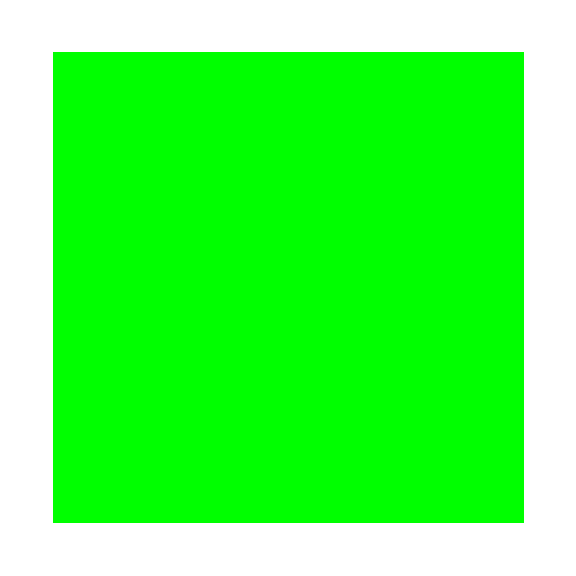

```mathematica
differences=MapThread[Not@*Equal,{CovMatrix50x30tabzSKA[[1]],Transpose[CovMatrix30x50tabzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixzSKA[[1]],Transpose[MultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

## COVARIANCE MATRIX + OCTUPOLE JOINT 10x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
CovMatrixOCT50Bx50FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrixOCT30Bx70FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-20B_80F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrixOCT50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrixOCT30Bx70FzSKA[[1,1,1]]
```

0.0000423384

```mathematica
MultiSplitCovMatrixOCTzSKA = Table[
Join[ArrayFlatten[{{CovMatrixOCT50Bx50FzSKA[[i]], CovMatrixOCT50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrixOCT30x50tabzSKA[[i]], CovMatrixOCT30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,648,648}

```mathematica
MultiSplitCovMatrixOCTzSKA[[All,325;;648,325;;648]]== CovMatrixOCT30Bx70FzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,1;;324,325;;648]]== CovMatrixOCT50x30tabzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,325;;648,1;;324]]== CovMatrixOCT30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrixOCT50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrixOCT30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrixOCT50x30tabzSKA[[i]] ==CovMatrixOCT30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

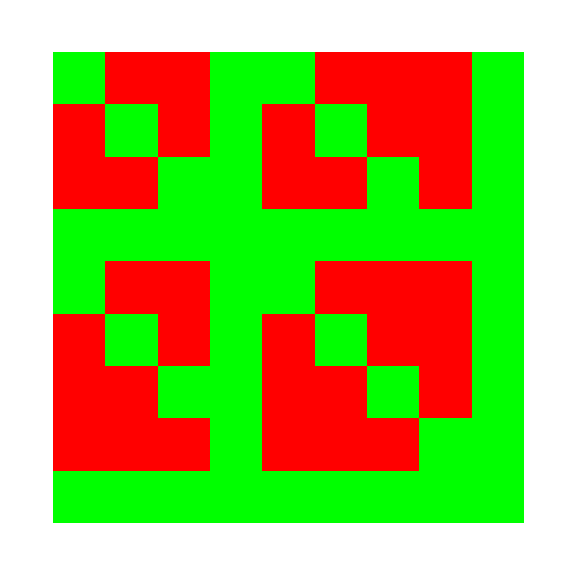

```mathematica
differences=MapThread[Not@*Equal,{CovMatrixOCT50x30tabzSKA[[1]],CovMatrixOCT30x50tabzSKA[[1]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT30x50tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixOCTzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixOCTzSKA[[1]],Transpose[MultiSplitCovMatrixOCTzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

# EXPORT

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,576,576}

{19,648,648}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_all_50x20_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_all_50x20_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixOCTzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
Exit[]
```